# Notebook for : General Relativity by Straumann

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
October 10, 2021

THIS IS NOT AT ALL OBVIOUS FROM THE TEXT.  IN THE FIRST PART OF THE PROBLEM a is a(t) which is time dependent.  Also e is e(t) and is time dependent.  After an enormous amount of grief one finds the first derivatives on the moments of inertia.  When you go to take the second derivatives you find you need an a dot, e dot, r dot and θ dot.  Two expressions are given for r dot and for θ dot.  What is implied, but not stated is that you now treat both a and e as constants.  I’m embarrassed to admit I don’t know why, and even more embarrassed to admit I’ve spend all god damn day on this.

```mathematica
(* Also See Will Theory and Experiment second edition page 276 for same discussion of binary pulsar coordinate system given on page 337 of Straumann and page 480 of Shapiro and Teukolsky.
Five orbital parameters (ι,Ω,a,e,ω) :
ι inclination angle
Ω called longitude of ascending node 
a semi major axis 
e eccentricity 
ω is the argument of the periastron 
ϕ is called true anamoly  which is called f in Will's test
 *)
```

Also Ξ is redefined as ρ on page 7.192 (Couldn’t find this definition to save my life... )
Also needs to be checked .. whether or not the definition should be Σ or Σ^2 in order to be consistent

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Related Papers

```mathematica
(* This Edition *) 
Hyperlink["General Relativity Straumann",
"https://www.springer.com/gp/book/9783642060137"]
```

[General Relativity Straumann](https://www.springer.com/gp/book/9783642060137)

```mathematica
Hyperlink["General Relativity Norbert Straumann",
"https://www.springer.com/gp/book/9789400754096"]
```

[General Relativity Norbert Straumann](https://www.springer.com/gp/book/9789400754096)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 9 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"] (* needed for geodesic equations of metric *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[OverHat[A]] , 
PasteButton[OverHat[X] ] , 
PasteButton[Superscript[β,φ]],
PasteButton[OverTilde[dV]],
PasteButton[OverTilde[dφ]],
PasteButton[Subscript[L,z]],
PasteButton[Subscript[S,r]],
PasteButton[Subscript[S,ϑ]]
}]
```

upuv6_shm43FrontEndObject[LinkObject["upuv6_shm", 3, 1]]43Untitled-5

```mathematica
Symbolize[Â]
Symbolize[X̂]
Symbolize[β^φ]
Symbolize[OverTilde[dV]]
Symbolize[OverTilde[dφ]]
Symbolize[Subscript[L, z]]
Symbolize[Subscript[S, r]]
Symbolize[Subscript[S, ϑ]]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[t]-> dt , 
Dt[u]-> du ,
 Dt[v] -> dv  , 
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz , 
Dt[ρ]-> dρ , 
Dt[φ]-> dφ
};
dtReplace // TableForm
```

Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[ρ]→dρ
Dt[φ]→dφ

## Chapter 4 Calculations: Equations 4.88 and 4.189 - 4.194

```mathematica
Clear[eq4pt88]
eq4pt88 = 
-dt^2+ dx^2+ L[u]^2( Exp[2β[u]] dy^2+  Exp[-2β[u]] dz^2 )
```

-dt^2+dx^2+(dz^2 ⅇ^(-2 β[u])+dy^2 ⅇ^(2 β[u])) L[u]^2

```mathematica
lineToMetric[ eq4pt88 , {dt,dx,dy,dz} ]  // MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (L(u))^2 ⅇ^(2 β(u)) | 0
0 | 0 | 0 | (L(u))^2 ⅇ^(-2 β(u)))

```mathematica
Clear[eq4pt88a]
eq4pt88a = { 
u == (1/(√2))(x-t) , 
v == (1/(√2))(x+t)
} ;
eq4pt88a  // TableForm
```

u==(-t+x)/(√2)
v==(t+x)/(√2)

```mathematica
Flatten[Solve[ eq4pt88a , {x,t} ]] // TableForm
```

x→u/(√2)+v/(√2)
t→1/2 (-√2 u+√2 v)

```mathematica
Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  // TableForm
```

dx→du/(√2)+dv/(√2)
dt→1/2 (-√2 du+√2 dv)

```mathematica
eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )
```

(du/(√2)+dv/(√2))^2-1/4 (-√2 du+√2 dv)^2+(dz^2 ⅇ^(-2 β[u])+dy^2 ⅇ^(2 β[u])) L[u]^2

```mathematica
eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )  // Expand
```

2 du dv+dz^2 ⅇ^(-2 β[u]) L[u]^2+dy^2 ⅇ^(2 β[u]) L[u]^2

```mathematica
Clear[metric4pt88]
metric4pt88 = 
lineToMetric[ ( eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )  // Expand  ) , {du,dv,dy,dz} ]  ;
metric4pt88 // MatrixForm // pdConv
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | (L(u))^2 ⅇ^(2 β(u)) | 0
0 | 0 | 0 | (L(u))^2 ⅇ^(-2 β(u)))

```mathematica
Clear[eq4pt189a]
eq4pt189a = 
a[t] == -((m1 m2)/(2 ℰ[t]))
```

a[t]==-(m1 m2)/(2 ℰ[t])

```mathematica
Clear[eq4pt189b]
eq4pt189b = 
ℯ[t]^2 == 1 + (2 ℰ[t] L[t]^2 (m1 + m2 ))/(m1^3 m2^3)
```

ℯ[t]^2==1+(2 (m1+m2) L[t]^2 ℰ[t])/(m1^3 m2^3)

```mathematica
Clear[eq4pt190a]
eq4pt190a = 
D[ eq4pt189a , t ]
```

a'[t]==(m1 m2 ℰ'[t])/(2 ℰ[t]^2)

```mathematica
Clear[eq4pt190b]
eq4pt190b = 
D[ eq4pt189b , t ]
```

2 ℯ[t] ℯ'[t]==(4 (m1+m2) L[t] ℰ[t] L'[t])/(m1^3 m2^3)+(2 (m1+m2) L[t]^2 ℰ'[t])/(m1^3 m2^3)

```mathematica
Clear[eq4pt191]
eq4pt191 = {
r[t] ==(a[t](1-ℯ[t]^2))/(1+ℯ[t] Cos[θ[t]]) , 
r1[t] == (m2/(m1+m2))r[t] , 
r2[t] == (m1/(m1+m2))r[t]
} ;
eq4pt191 // TableForm
```

r[t]==(a[t] (1-ℯ[t]^2))/(1+Cos[θ[t]] ℯ[t])
r1[t]==(m2 r[t])/(m1+m2)
r2[t]==(m1 r[t])/(m1+m2)

```mathematica
( eq4pt191[[2]] /. Equal-> Rule  ) 
( eq4pt191[[3]] /. Equal-> Rule  )
```

r1[t]→(m2 r[t])/(m1+m2)

r2[t]→(m1 r[t])/(m1+m2)

```mathematica
Clear[x1]
x1 =(  r1[t] /. ( eq4pt191[[2]] /. Equal-> Rule  )  ) Cos[θ[t]]
```

(m2 Cos[θ[t]] r[t])/(m1+m2)

```mathematica
Clear[x2]
x2 = ( r2[t] /. ( eq4pt191[[3]] /. Equal-> Rule  ) )  Cos[θ[t]]
```

(m1 Cos[θ[t]] r[t])/(m1+m2)

```mathematica
Clear[x]
x = { x1,x2 }
```

{(m2 Cos[θ[t]] r[t])/(m1+m2),(m1 Cos[θ[t]] r[t])/(m1+m2)}

```mathematica
Clear[y1]
y1 =(  r1[t] /. ( eq4pt191[[2]] /. Equal-> Rule  )  ) Sin[θ[t]]
```

(m2 r[t] Sin[θ[t]])/(m1+m2)

```mathematica
Clear[y2]
y2 = ( r2[t] /. ( eq4pt191[[3]] /. Equal-> Rule  ) )  Sin[θ[t]]
```

(m1 r[t] Sin[θ[t]])/(m1+m2)

```mathematica
Clear[y]
y = { y1 , y2 }
```

{(m2 r[t] Sin[θ[t]])/(m1+m2),(m1 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[𝓇1]
𝓇1 = {x1,y1}
```

{(m2 Cos[θ[t]] r[t])/(m1+m2),(m2 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[𝓇2]
𝓇2 = {x2,y2}
```

{(m1 Cos[θ[t]] r[t])/(m1+m2),(m1 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[ℐ]
ℐ = 
Table[ (m1  𝓇1 [[i]] 𝓇1 [[j]]  + m2 𝓇2 [[i]] 𝓇2 [[j]]  )  , {i,1,2}, {j,1,2} ]  // Expand // Simplify   ;
ℐ // MatrixForm
```

((m1 m2 Cos[θ[t]]^2 r[t]^2)/(m1+m2) | (m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]])/(m1+m2)
(m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]])/(m1+m2) | (m1 m2 r[t]^2 Sin[θ[t]]^2)/(m1+m2))

```mathematica
ℐ[[1,1]]
```

(m1 m2 Cos[θ[t]]^2 r[t]^2)/(m1+m2)

```mathematica
Clear[eq4pt193a]
eq4pt193a = 
L[t] == ((m1 m2)/(m1 + m2)) r[t]^2 θ'[t]  ;
```

```mathematica
(* How to solve equation 4pt193 *) 
Flatten[Solve[ ( ( ( Eliminate[ { eq4pt189a,eq4pt189b /.  ( eq4pt193a /. Equal-> Rule  )  }  , ℰ[t] ][[1]]  )  ) //.  ℯ[t]-> √(1-β[t]^2)  ) , θ'[t] ]][[2]]  /. β[t]-> √(1-ℯ[t]^2)
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Clear[eq4pt193] (* Clean this up a bit *) 
eq4pt193 = 
θ'[t] ==(( m1 + m2 )^(1/2)√a[t]  (1-ℯ[t]^2)^(1/2))/r[t]^2 ;
( eq4pt193  /. Equal-> Rule )
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Clear[eccentricitySimplify]
eccentricitySimplify = { 
ℯ[t]-> √(1-β[t]^2) , 
β[t] -> √(1-ℯ[t]^2) , 
ℯ-> √(1-β^2) , 
β -> √(1-ℯ^2)
} ;
eccentricitySimplify  // TableForm
```

ℯ[t]→√(1-β[t]^2)
β[t]→√(1-ℯ[t]^2)
ℯ→√(1-β^2)
β→√(1-ℯ^2)

```mathematica
(* Could use this for equation 4.193 *) 
( ( Flatten[Solve[ Eliminate[ { eq4pt189a,eq4pt189b } , ℰ[t] ] [[1]]  /. ( eq4pt193a  /. Equal-> Rule )  , θ'[t] ] ][[2]] // Simplify   )  /. eccentricitySimplify[[1]] // PowerExpand   ) /. eccentricitySimplify[[2]]
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]]
D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ] 

D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ]  /. Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]] /.( ( eq4pt193 /. ℯ[t]-> ℯ  /. a[t]-> a )  /. Equal-> Rule )  

Clear[eq4pt194a]
eq4pt194a = 
D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ]  /. Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]] /.( ( eq4pt193 /. ℯ[t]-> ℯ  /. a[t]-> a )  /. Equal-> Rule )   /. ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a  /. Equal-> Rule )
```

Cos[θ[t]]→(a-a ℯ^2-r[t])/(ℯ r[t])

r'[t]==(a ℯ (1-ℯ^2) Sin[θ[t]] θ'[t])/(1+ℯ Cos[θ[t]])^2

r'[t]==(a^(3/2) √(m1+m2) ℯ (1-ℯ^2)^(3/2) Sin[θ[t]])/((1+ℯ Cos[θ[t]])^2 r[t]^2)

r'[t]==(√(m1+m2) ℯ Sin[θ[t]])/(√a √(1-ℯ^2))

```mathematica
(* See above for derivation *) 
Clear[eq4pt194]
eq4pt194 = 
r'[t] ==(ℯ[t] Sin[θ[t]] ( m1 + m2 )^(1/2))/(a[t]^(1/2)(1-ℯ[t]^2)^(1/2))
```

r'[t]==(√(m1+m2) Sin[θ[t]] ℯ[t])/(√a[t] √(1-ℯ[t]^2))

```mathematica
Clear[rDotReplace]
rDotReplace = 
r'[t] -> (ℯ[t] Sin[θ[t]] ( m1 + m2 )^(1/2))/(a[t]^(1/2) (1-ℯ[t]^2)^(1/2))
```

r'[t]→(√(m1+m2) Sin[θ[t]] ℯ[t])/(√a[t] √(1-ℯ[t]^2))

```mathematica
Clear[thetaDotReplace]
thetaDotReplace = 
θ'[t]-> (( m1 + m2 )^(1/2) a[t]^(1/2) (1-ℯ[t]^2)^(1/2))/r[t]^2
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Flatten[Solve[ eq4pt191[[1]] , θ[t] ] ][[1]]  /. C[1]-> 0
```

θ[t]→-ArcCos[(a[t]-r[t]-a[t] ℯ[t]^2)/(r[t] ℯ[t])]

```mathematica
Flatten[Solve[ eq4pt191[[1]] , ℯ[t] ] ][[1]]
```

ℯ[t]→(-Cos[θ[t]] r[t]-√(Cos[θ[t]]^2 r[t]^2-4 a[t] (-a[t]+r[t])))/(2 a[t])

```mathematica
Flatten[Solve[ eq4pt191[[1]] , a[t] ] ][[1]]
```

a[t]→-(r[t] (1+Cos[θ[t]] ℯ[t]))/(-1+ℯ[t]^2)

```mathematica
Clear[cosThetaReplace]
cosThetaReplace = 
Collect[ ( Flatten[Solve[ ( eq4pt191[[1]] /. Cos[θ[t]] -> β ) , β ]][[1]]  /. β-> Cos[θ[t] ] ) , a[t] ]
```

Cos[θ[t]]→-1/ℯ[t]+(a[t] (1-ℯ[t]^2))/(r[t] ℯ[t])

```mathematica
Clear[aReplace]
aReplace = 
Flatten[Solve[ eq4pt191[[1]] , a[t] ] ][[1]]
```

a[t]→-(r[t] (1+Cos[θ[t]] ℯ[t]))/(-1+ℯ[t]^2)

```mathematica
Clear[rReplace]
rReplace = 
( eq4pt191[[1]] /. Equal-> Rule  )
```

r[t]→(a[t] (1-ℯ[t]^2))/(1+Cos[θ[t]] ℯ[t])

```mathematica
(* 
For the following calculations see page 496 of Problem Book In Relativity and Gravitation
*)
```

## OverDot[I_xx] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[1,1]] , t ]
```

(2 m1 m2 Cos[θ[t]]^2 r[t] r'[t])/(m1+m2)-(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]
```

-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(β[t]^2))/(√(m1+m2))+(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(1-β[t]^2))/(√(m1+m2) √a[t] √(β[t]^2))

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand
```

-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] β[t])/(√(m1+m2))+(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(1-β[t]^2))/(√(m1+m2) √a[t] β[t])

```mathematica
( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]]
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(ℯ[t]^2))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify
```

(m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  )
```

(m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IxxDotNumerator]
IxxDotNumerator = Numerator[(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ) ]
```

m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2))

```mathematica
Clear[IxxDotDenominator]
IxxDotDenominator = 
Denominator[(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ) ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
IxxDotNumerator /. aReplace // Expand // Simplify  // TrigExpand
```

-2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]]

```mathematica
Clear[IxxDot]
IxxDot = 
( IxxDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  )/IxxDotDenominator
```

-(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195a]
eq4pt195a = 
IxxDot
```

-(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## OverDot[I_yy] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[2,2]] , t]
```

(2 m1 m2 r[t] Sin[θ[t]]^2 r'[t])/(m1+m2)+(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]
```

(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(β[t]^2))/(√(m1+m2))+(2 m1 m2 r[t] Sin[θ[t]]^3 √(1-β[t]^2))/(√(m1+m2) √a[t] √(β[t]^2))

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand
```

(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] β[t])/(√(m1+m2))+(2 m1 m2 r[t] Sin[θ[t]]^3 √(1-β[t]^2))/(√(m1+m2) √a[t] β[t])

```mathematica
( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]]
```

(2 m1 m2 r[t] Sin[θ[t]]^3 √(ℯ[t]^2))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify
```

-(2 m1 m2 (-r[t] Sin[θ[t]]^3 ℯ[t]+a[t] Cos[θ[t]] Sin[θ[t]] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IyyDotNumerator]
IyyDotNumerator   = 
Numerator[ ( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ]
```

-2 m1 m2 (-r[t] Sin[θ[t]]^3 ℯ[t]+a[t] Cos[θ[t]] Sin[θ[t]] (-1+ℯ[t]^2))

```mathematica
Clear[IyyDotDenominator]
IyyDotDenominator    = 
Denominator[ ( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
IyyDotNumerator /. aReplace // Expand  // Simplify
```

2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t])

```mathematica
Clear[IyyDot]
IyyDot = 
( IyyDotNumerator /. aReplace // Expand  // Simplify  )/IyyDotDenominator
```

(2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195d]
eq4pt195d = 
IyyDot
```

(2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## OverDot[I_xy] = OverDot[I_yx] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[1,2]] , t ]
```

(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t])/(m1+m2)+(m1 m2 Cos[θ[t]]^2 r[t]^2 θ'[t])/(m1+m2)-(m1 m2 r[t]^2 Sin[θ[t]]^2 θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace
```

(m1 m2 √a[t] Cos[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))-(m1 m2 √a[t] Sin[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))+(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace
```

(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]]^2 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(m1 m2 √a[t] Cos[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))-(m1 m2 √a[t] Sin[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify
```

(m1 m2 (r[t] Sin[θ[t]] Sin[2 θ[t]] ℯ[t]-a[t] Cos[2 θ[t]] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IxyDotNumerator]
IxyDotNumerator = 
Numerator[D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify  ]
```

m1 m2 (r[t] Sin[θ[t]] Sin[2 θ[t]] ℯ[t]-a[t] Cos[2 θ[t]] (-1+ℯ[t]^2))

```mathematica
Clear[IxyDotDenominator]
IxyDotDenominator = 
Denominator[ D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify  ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
Collect[ ( IxyDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  ) ,m1 m2 r[t] ]
```

m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t])

```mathematica
Clear[IxyDot]
IxyDot = 
Collect[ ( IxyDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  ) ,m1 m2 r[t] ]/IxyDotDenominator
```

(m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195g]
eq4pt195g = 
IxyDot
```

(m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## I_xx^(..) Calculation and Reduction

```mathematica
Clear[IxxDoubleDot]
IxxDoubleDot = 
( D[( IxxDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

(m1 m2 (3 ℯ Cos[θ[t]]+4 Cos[2 θ[t]]+ℯ Cos[3 θ[t]]))/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxxDoubleDot  == ( - 2 m1 m2 )/(a(1-ℯ^2))( Cos[2θ[t]] + ℯ  Cos[θ[t]]^3)  // Expand  // Simplify
```

True

## I_yy^(..) Calculation and Reduction

```mathematica
Clear[IyyDoubleDot]
IyyDoubleDot = 
( D[( IyyDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

-(m1 m2 (7 ℯ Cos[θ[t]]+4 Cos[2 θ[t]]+ℯ (4 ℯ+Cos[3 θ[t]])))/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IyyDoubleDot  == (  2 m1 m2 )/(a(1-ℯ^2))( Cos[2θ[t]] +ℯ  Cos[θ[t]]+ ℯ  Cos[θ[t]]^3+ ℯ^2)  // Expand  // Simplify
```

True

## I_xy^(..) Calculation and Reduction

```mathematica
Clear[IxyDoubleDot]
IxyDoubleDot = 
( D[( IxyDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

(m1 m2 (4 Cos[θ[t]]+ℯ (3+Cos[2 θ[t]])) Sin[θ[t]])/(a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxyDoubleDot == ( - 2 m1 m2 )/(a(1-ℯ^2))( Sin[2θ[t]] + ℯ  Sin[θ[t]] + ℯ Sin[θ[t]] Cos[θ[t]]^2) // Expand // Simplify
```

True

## I_xx^(...) Calculation and Reduction

```mathematica
Clear[IxxTripleDot]
IxxTripleDot = 
D[ IxxDoubleDot , t ]   // Simplify
```

-(m1 m2 (4+3 ℯ Cos[θ[t]]) Sin[2 θ[t]] θ'[t])/(a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxxTripleDot ==  (  2 m1 m2 )/(a(1-ℯ^2))( 2 Sin[2θ[t]] + 3ℯ Cos[θ[t]]^2 Sin[θ[t]] ) θ'[t]  // Simplify
```

True

## I_yy^(...) Calculation and Reduction

```mathematica
Clear[IyyTripleDot]
IyyTripleDot = 
Collect[ D[ IyyDoubleDot , t ] , θ'[t] ]
```

-(m1 m2 (-7 ℯ Sin[θ[t]]-8 Sin[2 θ[t]]-3 ℯ Sin[3 θ[t]]) θ'[t])/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IyyTripleDot  ==  ( - 2 m1 m2 )/(a(1-ℯ^2))( 2 Sin[2θ[t]] + ℯ Sin[θ[t]] +  3 ℯ Cos[θ[t]]^2 Sin[θ[t]]) θ'[t]  // Simplify
```

True

## I_xy^(...) Calculation and Reduction

```mathematica
Clear[IxyTripleDot]
IxyTripleDot = 
 D[ IxyDoubleDot , t ]   // Together // Simplify
```

(m1 m2 (5 ℯ Cos[θ[t]]+8 Cos[2 θ[t]]+3 ℯ Cos[3 θ[t]]) θ'[t])/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxyTripleDot == ( - 2 m1 m2 )/(a(1-ℯ^2))( 2 Cos[2θ[t]] - ℯ Cos[θ[t]] +  3 ℯ Cos[θ[t]]^3) θ'[t]   // Expand  // Simplify
```

True

## I^(...) Calculation and Reduction

```mathematica
Clear[ItripleDot]
ItripleDot = 
IxxTripleDot+IyyTripleDot // Expand  // TrigExpand
```

(2 m1 m2 ℯ Sin[θ[t]] θ'[t])/(a (-1+ℯ^2))

## More Chapter 4 Calculations: Equations 4.196 - 4.200

```mathematica
(* This just looks different due to factoring double angle identity... expanding it out and collecting gives expression in book as shown below *) 
Clear[Lgw]
Lgw = 
Collect[ (1/5)* ( ( IxxTripleDot^2+ 2*IxyTripleDot^2+IyyTripleDot^2-(1/3)ItripleDot^2 )  // Expand // Simplify  ) // TrigExpand  , θ'[t] ]   // FullSimplify
```

(4 m1^2 m2^2 (24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]) θ'[t]^2)/(15 a^2 (-1+ℯ^2)^2)

```mathematica
Lgw[[1;;5]]
Lgw[[6]] 
Lgw[[7]]
```

(4 m1^2 m2^2)/(15 a^2 (-1+ℯ^2)^2)

24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]

θ'[t]^2

```mathematica
Lgw[[6]] == 2*( 12(1+ℯ Cos[θ[t]])^2 + ℯ^2 Sin[θ[t]]^2 )// Expand // Simplify
```

True

```mathematica
Clear[eq4pt196]
eq4pt196 = 
T ==(2 π a^(3/2))/(m1+m2)^(1/2)
```

T==(2 a^(3/2) π)/(√(m1+m2))

```mathematica
Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ
```

(4 m1^2 m2^2 √(m1+m2) (1+ℯ Cos[θ[t]])^2 (24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]))/(15 a^(7/2) (1-ℯ^2)^(3/2) (-1+ℯ^2)^2)

```mathematica
Integrate[ ( Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ  /. θ[t]-> θ  ) , {θ,0,2π}]
```

(2 m1^2 m2^2 √(m1+m2) π (96+292 ℯ^2+37 ℯ^4))/(15 a^(7/2) (1-ℯ^2)^(7/2))

```mathematica
Clear[eq4pt197] (* Factoring out 96 as in the next line will give the form in the book *) 
eq4pt197 = 
( (1/T) /. ( eq4pt196  /. Equal-> Rule )  )* Integrate[ ( Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ  /. θ[t]-> θ ) , {θ,0,2π}]
```

(m1^2 m2^2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^5 (1-ℯ^2)^(7/2))

```mathematica
( 96+292 ℯ^2+37 ℯ^4 ) / 96  // Expand
```

1+(73 ℯ^2)/24+(37 ℯ^4)/96

```mathematica
Clear[LgwAveraged]
LgwAveraged = 
eq4pt197
```

(m1^2 m2^2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^5 (1-ℯ^2)^(7/2))

```mathematica
Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]]
eq4pt190a
```

ℰ[t]→-(m1 m2)/(2 a[t])

a'[t]==(m1 m2 ℰ'[t])/(2 ℰ[t]^2)

```mathematica
eq4pt190a /. Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]]
```

a'[t]==(2 a[t]^2 ℰ'[t])/(m1 m2)

```mathematica
(* factoring out a 96 will give their exact expression *) 
Clear[eq4pt198]
eq4pt198 = 
( eq4pt190a /. Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]] ) /. ℰ'[t] -> (-LgwAveraged )  /. a[t]-> a
```

a'[t]==-(2 m1 m2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^3 (1-ℯ^2)^(7/2))

```mathematica
( eq4pt196 /. T-> T[t] /. a-> a[t]  ) 
( eq4pt196 /. T-> T[t] /. a-> a[t]  )[[2]]
```

T[t]==(2 π a[t]^(3/2))/(√(m1+m2))

(2 π a[t]^(3/2))/(√(m1+m2))

```mathematica
D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] 
D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] [[2]]
```

T'[t]==(3 π √a[t] a'[t])/(√(m1+m2))

(3 π √a[t] a'[t])/(√(m1+m2))

```mathematica
(D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] [[2]])/(( eq4pt196 /. T-> T[t] /. a-> a[t]  )[[2]])
```

(3 a'[t])/(2 a[t])

```mathematica
Clear[eq4pt199]
eq4pt199 = 
(3/2)eq4pt198[[2]]/a
```

-(m1 m2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(5 a^4 (1-ℯ^2)^(7/2))

```mathematica
( Numerator[eq4pt199][[5]] / 96  // Expand  )
```

1+(73 ℯ^2)/24+(37 ℯ^4)/96

```mathematica
Denominator[eq4pt199][[3]]
```

(1-ℯ^2)^(7/2)

```mathematica
Clear[eq4pt200]
eq4pt200 = 
f[ℯ] == ( Numerator[eq4pt199][[5]] / 96  // Expand  )/(Denominator[eq4pt199][[3]])
```

f[ℯ]==(1+(73 ℯ^2)/24+(37 ℯ^4)/96)/((1-ℯ^2)^(7/2))

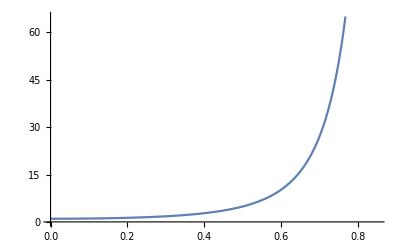

```mathematica
Plot[ eq4pt200[[2]] , {ℯ,0,0.85} ]
```

```mathematica
Clear[eq4pt201a]
eq4pt201a = { 
 m == m1 + m2 , 
η == (m1 m2)/(m1+m2)^2 , 
ℳ == η^(5/3) m 
} ;
```

```mathematica
eq4pt201a[[1]] /. Equal-> Rule 
eq4pt201a[[2]] /. Equal-> Rule
```

m→m1+m2

η→(m1 m2)/(m1+m2)^2

```mathematica
eq4pt201a[[3]] 
eq4pt201a[[3]] /. ( eq4pt201a[[1]] /. Equal-> Rule  ) /. ( eq4pt201a[[2]] /. Equal-> Rule  )  // PowerExpand // Simplify
```

ℳ==m η^(5/3)

ℳ==(m1^(5/3) m2^(5/3))/(m1+m2)^(7/3)

## Chapter 5: Equation 184 - 189

```mathematica
Clear[eq5pt184]
eq5pt184 = 
K == { Cos[Ω] , Sin[Ω] , 0 }
```

K=={Cos[Ω],Sin[Ω],0}

```mathematica
Clear[eq5pt185]
eq5pt185 = 
𝒩 == {  Sin[ι]  Sin[Ω] ,- Sin[ι]  Cos[Ω],Cos[ι] }
```

𝒩=={Sin[ι] Sin[Ω],-Cos[Ω] Sin[ι],Cos[ι]}

```mathematica
θ == ω+ϕ
```

θ==ϕ+ω

```mathematica
Flatten[ Solve[ θ == ω+ϕ , ϕ] ][[1]]
```

ϕ→θ-ω

```mathematica
Cos[(ω+ϕ)]( K /.(  eq5pt184  /. Equal-> Rule )  )
```

{Cos[ϕ+ω] Cos[Ω],Cos[ϕ+ω] Sin[Ω],0}

```mathematica
Sin[(ω+ϕ)]Cross[ ( 𝒩 /. ( eq5pt185  /. Equal-> Rule ) ) , (  K /.(  eq5pt184  /. Equal-> Rule )  ) ]
```

{-Cos[ι] Sin[ϕ+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ϕ+ω],Sin[ϕ+ω] (Cos[Ω]^2 Sin[ι]+Sin[ι] Sin[Ω]^2)}

```mathematica
Clear[eq5pt186]
eq5pt186 = 
Cos[(ω+ϕ)]( K /.(  eq5pt184  /. Equal-> Rule )  )  + Sin[(ω+ϕ)]Cross[ ( 𝒩 /. ( eq5pt185  /. Equal-> Rule ) ) , (  K /.(  eq5pt184  /. Equal-> Rule )  ) ]
```

{Cos[ϕ+ω] Cos[Ω]-Cos[ι] Sin[ϕ+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ϕ+ω]+Cos[ϕ+ω] Sin[Ω],Sin[ϕ+ω] (Cos[Ω]^2 Sin[ι]+Sin[ι] Sin[Ω]^2)}

```mathematica
Clear[eq5pt187]
eq5pt187 = 
x1  == ( r1 * eq5pt186  ) /. Flatten[ Solve[ θ == ω+ϕ , ϕ] ][[1]]  // Expand // Simplify  ;
( eq5pt187  /. Equal-> Rule )
```

(m2 Cos[θ[t]] r[t])/(m1+m2)→{r1 Cos[θ] Cos[Ω]-r1 Cos[ι] Sin[θ] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[θ]+r1 Cos[θ] Sin[Ω],r1 Sin[θ] Sin[ι]}

```mathematica
Clear[eq5pt188]
eq5pt188 = 
eq5pt187[[2]][[3]] /. (  θ == ω+ϕ /. Equal-> Rule )
```

((m2 Cos[(ϕ+ω)[t]] r[t])/(m1+m2)=={r1 Cos[ϕ+ω] Cos[Ω]-r1 Cos[ι] Sin[ϕ+ω] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[ϕ+ω]+r1 Cos[ϕ+ω] Sin[Ω],r1 Sin[ι] Sin[ϕ+ω]})⟦3⟧

r1 Sin[ι] Sin[ϕ+ω]

```mathematica
Clear[eq5pt189]
eq5pt189 = 
r1 ==(a1(1-ℯ^2))/(1+ℯ Cos[θ]) ;
( eq5pt189  /. Equal-> Rule  )
```

r1→(a1 (1-ℯ^2))/(1+ℯ Cos[θ])

## Check This

```mathematica
x1 /. ( eq5pt187  /. Equal-> Rule )   /. θ-> ( ω+ϕ)
```

{r1 Cos[ϕ+ω] Cos[Ω]-r1 Cos[ι] Sin[ϕ+ω] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[ϕ+ω]+r1 Cos[ϕ+ω] Sin[Ω],r1 Sin[ι] Sin[ϕ+ω]}

```mathematica
( eq5pt189  /. Equal-> Rule  )
```

r1→(a1 (1-ℯ^2))/(1+ℯ Cos[θ])

```mathematica
Clear[orbitPath]
orbitPath = 
( x1 /. ( eq5pt187  /. Equal-> Rule )   /. θ-> ( ω+ϕ)   ) /. ( eq5pt189  /. Equal-> Rule  )
```

{(a1 (1-ℯ^2) Cos[ϕ+ω] Cos[Ω])/(1+ℯ Cos[θ])-(a1 (1-ℯ^2) Cos[ι] Sin[ϕ+ω] Sin[Ω])/(1+ℯ Cos[θ]),(a1 (1-ℯ^2) Cos[ι] Cos[Ω] Sin[ϕ+ω])/(1+ℯ Cos[θ])+(a1 (1-ℯ^2) Cos[ϕ+ω] Sin[Ω])/(1+ℯ Cos[θ]),(a1 (1-ℯ^2) Sin[ι] Sin[ϕ+ω])/(1+ℯ Cos[θ])}

```mathematica
orbitPath /. ℯ-> 0  /. a1-> 3
```

{3 Cos[ϕ+ω] Cos[Ω]-3 Cos[ι] Sin[ϕ+ω] Sin[Ω],3 Cos[ι] Cos[Ω] Sin[ϕ+ω]+3 Cos[ϕ+ω] Sin[Ω],3 Sin[ι] Sin[ϕ+ω]}

```mathematica
Manipulate[ 
ParametricPlot3D[
Evaluate[orbitPath /. ℯ-> 0.5  /. a1-> 3   /. Ω-> lan /. ω-> aop /. ι-> inc ] ,  {ϕ,0, phiMax}  , AxesLabel-> {x,y,z} , PlotRange-> {-5,5},PlotStyle->Directive[Blue,Opacity[0.74]],AxesLabel->{x,y,z},LabelStyle->{20,Bold},ImageSize->Large,ViewPoint->{11,2,3},AxesStyle->Thick,Boxed->False,AxesOrigin->{0,0,0}
 ]  , {phiMax, 0.01 , 6.3 }  , 
{lan,0,2π } , {aop,0,2π} , {inc,0,π} ]
```

## More Chapter 5 Calculations: Equations 5.190

```mathematica
Clear[eq5pt190]
eq5pt190 =  { 
ℯ^2 == 1 + (2 ℰ L^2 (m1 + m2 ))/(m1^3 m2^3) , 
a(1-ℯ^2) == (L^2(m1+m2))/(G m1 m2)
} ;
eq5pt190  // TableForm
```

ℯ^2==1+(2 L^2 (m1+m2) ℰ)/(m1^3 m2^3)
a (1-ℯ^2)==(L^2 (m1+m2))/(G m1 m2)

```mathematica
Clear[eq5pt190a]
eq5pt190a = { 
a1 == (m2 a)/M , 
M == m1 + m2 , 
L == ((m1 m2)/(m1 + m2)) r^2 ϕ'[t]
} ;
eq5pt190a  // TableForm
```

a1==(a m2)/M
M==m1+m2
L==(m1 m2 r^2 ϕ'[t])/(m1+m2)

```mathematica
eq5pt190[[2]]
( eq5pt190a [[3]] /. Equal-> Rule  )
```

a (1-ℯ^2)==(L^2 (m1+m2))/(G m1 m2)

L→(m1 m2 r^2 ϕ'[t])/(m1+m2)

```mathematica
eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  )
```

a (1-ℯ^2)==(m1 m2 r^4 ϕ'[t]^2)/(G (m1+m2))

```mathematica
eq5pt190a [[1]]
eq5pt190a [[2]]
Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ] // TableForm
```

a1==(a m2)/M

M==m1+m2

m1→((a-a1) M)/a
m2→(a1 M)/a

```mathematica
( eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  ) ) /. Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ]
```

a (1-ℯ^2)==((a-a1) a1 M^2 r^4 ϕ'[t]^2)/(a^2 G (((a-a1) M)/a+(a1 M)/a))

```mathematica
(* Redo this... *) 

Flatten[Solve[ ( eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  ) ) /. Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ]  , ϕ'[t] ]]  // Expand // Simplify  // PowerExpand  // TableForm
```

ϕ'[t]→(ⅈ a^(3/2) √G √(-1+ℯ^2))/(√(a-a1) √a1 √M r^2)
ϕ'[t]→-(ⅈ a^(3/2) √G √(-1+ℯ^2))/(√(a-a1) √a1 √M r^2)

## Weyl Line Element and Metric Equation 7.140

```mathematica
Clear[eq7pt140]
eq7pt140 = 
-(ρ^2/X )dt^2+ X*( dφ + A dt)^2 + (1/X) Exp[2 h] ( dρ^2+dz^2)
```

((dz^2+dρ^2) ⅇ^(2 h))/X+(A dt+dφ)^2 X-(dt^2 ρ^2)/X

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 

Clear[metric7pt140a]
metric7pt140a =
lineToMetric[eq7pt140,{dt,dφ,dρ,dz}]  ;
metric7pt140a// MatrixForm // pdConv
```

(A^2 X-ρ^2/X | A X | 0 | 0
A X | X | 0 | 0
0 | 0 | ⅇ^(2 h)/X | 0
0 | 0 | 0 | ⅇ^(2 h)/X)

```mathematica
Clear[eq7pt140a]
eq7pt140a = {
X ->  X[ρ,z] , 
A-> A[ρ,z],
h ->  h[ρ,z]
}  ;
eq7pt140a  // TableForm
```

X→X[ρ,z]
A→A[ρ,z]
h→h[ρ,z]

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 

Clear[metric7pt140]
metric7pt140 =
lineToMetric[eq7pt140,{dt,dφ,dρ,dz}]  /. eq7pt140a   ;
metric7pt140 // MatrixForm // pdConv
```

((A(ρ,z))^2 X(ρ,z)-ρ^2/(X(ρ,z)) | A(ρ,z) X(ρ,z) | 0 | 0
A(ρ,z) X(ρ,z) | X(ρ,z) | 0 | 0
0 | 0 | ⅇ^(2 h(ρ,z))/(X(ρ,z)) | 0
0 | 0 | 0 | ⅇ^(2 h(ρ,z))/(X(ρ,z)))

## Calculation of Tensors Associated With Metric 7.140

```mathematica
Clear[input7pt140] 
input7pt140[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList7pt140];
tensorList7pt140 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList7pt140[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList7pt140[[2]]  = 
ChristoffelSymbol[ tensorList7pt140[[1]] , ActWith-> Simplify] ;
tensorList7pt140[[3]] = 
RiemannTensor[ tensorList7pt140[[1]] , ActWithNested-> Simplify ];
tensorList7pt140[[4]] = 
RicciTensor[ tensorList7pt140[[1]] , ActWith-> Simplify ] ;
tensorList7pt140[[5]] = 
RicciScalar[ tensorList7pt140[[1]] , ActWith-> Simplify ] ;
(*tensorList7pt140[[6]] = 
KretschmannScalar[ tensorList7pt140[[1]] , ActWith-> Simplify] ; *) 
tensorList7pt140[[7]] = 
EinsteinTensor[ tensorList7pt140[[1]] , ActWith-> Simplify] ;  
tensorList7pt140[[8]] = 
WeylTensor[ tensorList7pt140[[1]] , ActWith-> Simplify ] ;
(* tensorList7pt140[[9]] = 
CottonTensor[ tensorList7pt140[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 
(* Last timing took 15.53 for all tensors *) 
input7pt140[ "metric7pt140", metric7pt140, "Weyl","g^weyl",{t,φ,ρ,z}, "Greek"] // Timing
```

{14.8001,Null}

```mathematica
tensorList7pt140
```

{(g^weyl)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric7pt140,G_αβ^,C_αβγδ^,cottonmetric7pt140}

```mathematica
tensorList7pt140[[1]] 
TensorName[tensorList7pt140[[1]]] 
TensorValues[tensorList7pt140[[1]]] // MatrixForm // pdConv
```

(g^weyl)_αβ^

Weyl

((A(ρ,z))^2 X(ρ,z)-ρ^2/(X(ρ,z)) | A(ρ,z) X(ρ,z) | 0 | 0
A(ρ,z) X(ρ,z) | X(ρ,z) | 0 | 0
0 | 0 | ⅇ^(2 h(ρ,z))/(X(ρ,z)) | 0
0 | 0 | 0 | ⅇ^(2 h(ρ,z))/(X(ρ,z)))

```mathematica
tensorList7pt140[[2]] 
TensorName[tensorList7pt140[[2]]] 
TensorValues[tensorList7pt140[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolWeyl

((0
0
-(A(ρ,z) (X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/(2 ρ^2)-((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))+1/ρ
-(A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z))/(2 ρ^2 X(ρ,z))) | (0
0
-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/(2 ρ^2)
-((X(ρ,z))^2 (∂A(ρ,z))/(∂z))/(2 ρ^2)) | (-(A(ρ,z) (X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/(2 ρ^2)-((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))+1/ρ
-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/(2 ρ^2)
0
0) | (-(A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z))/(2 ρ^2 X(ρ,z))
-((X(ρ,z))^2 (∂A(ρ,z))/(∂z))/(2 ρ^2)
0
0)
(0
0
1/2 (((A(ρ,z))^2 (X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/ρ^2+A(ρ,z) ((2 (∂X(ρ,z))/(∂ρ))/(X(ρ,z))-2/ρ)+(∂A(ρ,z))/(∂ρ))
1/2 (((A(ρ,z))^2 (X(ρ,z))^2)/ρ^2+1) (∂A(ρ,z))/(∂z)+(A(ρ,z) (∂X(ρ,z))/(∂z))/(X(ρ,z))) | (0
0
((A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂ρ))/ρ^2+(∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))
((A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z))/ρ^2+(∂X(ρ,z))/(∂z))/(2 X(ρ,z))) | (1/2 (((A(ρ,z))^2 (X(ρ,z))^2 (∂A(ρ,z))/(∂ρ))/ρ^2+A(ρ,z) ((2 (∂X(ρ,z))/(∂ρ))/(X(ρ,z))-2/ρ)+(∂A(ρ,z))/(∂ρ))
((A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂ρ))/ρ^2+(∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))
0
0) | (1/2 (((A(ρ,z))^2 (X(ρ,z))^2)/ρ^2+1) (∂A(ρ,z))/(∂z)+(A(ρ,z) (∂X(ρ,z))/(∂z))/(X(ρ,z))
((A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z))/ρ^2+(∂X(ρ,z))/(∂z))/(2 X(ρ,z))
0
0)
(-(ⅇ^(-2 h(ρ,z)) (2 A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂ρ)+(A(ρ,z))^2 (X(ρ,z))^2 (∂X(ρ,z))/(∂ρ)+ρ^2 (∂X(ρ,z))/(∂ρ)-2 ρ X(ρ,z)))/(2 X(ρ,z))
-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (A(ρ,z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂ρ))
0
0) | (-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (A(ρ,z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂ρ))
-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (∂X(ρ,z))/(∂ρ)
0
0) | (0
0
(∂h(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))
(∂h(ρ,z))/(∂z)-((∂X(ρ,z))/(∂z))/(2 X(ρ,z))) | (0
0
(∂h(ρ,z))/(∂z)-((∂X(ρ,z))/(∂z))/(2 X(ρ,z))
((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))-(∂h(ρ,z))/(∂ρ))
(-(ⅇ^(-2 h(ρ,z)) (2 A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z)+(A(ρ,z))^2 (X(ρ,z))^2 (∂X(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z)))/(2 X(ρ,z))
-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (A(ρ,z) (∂X(ρ,z))/(∂z)+X(ρ,z) (∂A(ρ,z))/(∂z))
0
0) | (-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (A(ρ,z) (∂X(ρ,z))/(∂z)+X(ρ,z) (∂A(ρ,z))/(∂z))
-1/2 ⅇ^(-2 h(ρ,z)) X(ρ,z) (∂X(ρ,z))/(∂z)
0
0) | (0
0
((∂X(ρ,z))/(∂z))/(2 X(ρ,z))-(∂h(ρ,z))/(∂z)
(∂h(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))) | (0
0
(∂h(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂ρ))/(2 X(ρ,z))
(∂h(ρ,z))/(∂z)-((∂X(ρ,z))/(∂z))/(2 X(ρ,z))))

```mathematica
tensorList7pt140[[3]] 
TensorName[tensorList7pt140[[3]]] 
TensorValues[tensorList7pt140[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorWeyl

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 (-((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))))-(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3-(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ)+1/4 ((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3+(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ)
0 | 0 | 0 | 0) | (0 | (ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)+2 ρ X(ρ,z) (∂X(ρ,z))/(∂ρ)))/(4 X(ρ,z)) | 0 | 0
-(ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)+2 ρ X(ρ,z) (∂X(ρ,z))/(∂ρ)))/(4 X(ρ,z)) | 0 | 0 | 0
0 | 0 | 0 | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))+1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))
0 | 0 | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 0) | (0 | 0 | (2 ρ A(ρ,z) (X(ρ,z))^3 (ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))+(A(ρ,z))^2 (X(ρ,z))^2 ((X(ρ,z))^4 (-((∂A(ρ,z))/(∂ρ))^2)-2 ρ^2 X(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+ρ^2 ((∂X(ρ,z))/(∂z))^2)+ρ^2 (-3 (X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ X(ρ,z) (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(1-ρ (∂h(ρ,z))/(∂ρ)) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂ρ^2))-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂ρ)+ρ^2 (((∂X(ρ,z))/(∂z))^2+2 ((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^3) | 1/4 ((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3+(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ)
0 | 0 | 1/4 (-(2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ-2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))-(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))
-(2 ρ A(ρ,z) (X(ρ,z))^3 (ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))+(A(ρ,z))^2 (X(ρ,z))^2 ((X(ρ,z))^4 (-((∂A(ρ,z))/(∂ρ))^2)-2 ρ^2 X(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+ρ^2 ((∂X(ρ,z))/(∂z))^2)+ρ^2 (-3 (X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ X(ρ,z) (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(1-ρ (∂h(ρ,z))/(∂ρ)) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂ρ^2))-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂ρ)+ρ^2 (((∂X(ρ,z))/(∂z))^2+2 ((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^3) | 1/4 ((2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ+2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 0 | 0
1/4 (-((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))))-(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3-(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0) | (0 | 0 | 1/4 ((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3+(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | 1/4 (-X(ρ,z) (4 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+(∂^2 A(ρ,z))/(∂z^2))-4 A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+3 ((∂A(ρ,z))/(∂z))^2)+2 A(ρ,z) (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+((A(ρ,z))^2 ((∂X(ρ,z))/(∂ρ))^2+4 ρ (∂h(ρ,z))/(∂ρ))/(X(ρ,z))-((A(ρ,z))^2 (X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2+(2 ρ (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(ρ (∂h(ρ,z))/(∂ρ)+1) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)))/(X(ρ,z))^2+(ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(X(ρ,z))^3)
0 | 0 | -(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 1/4 (A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))+2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))
1/4 (-((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))))-(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3-(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 0 | 0
1/4 (X(ρ,z) (4 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+(∂^2 A(ρ,z))/(∂z^2))-4 A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+3 ((∂A(ρ,z))/(∂z))^2)-2 A(ρ,z) (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-((A(ρ,z))^2 ((∂X(ρ,z))/(∂ρ))^2+4 ρ (∂h(ρ,z))/(∂ρ))/(X(ρ,z))+((A(ρ,z))^2 (X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-(2 ρ (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(ρ (∂h(ρ,z))/(∂ρ)+1) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)))/(X(ρ,z))^2-(ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(X(ρ,z))^3) | 1/4 (-A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))-2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))+5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)) | 0 | 0)
(0 | -(ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)+2 ρ X(ρ,z) (∂X(ρ,z))/(∂ρ)))/(4 X(ρ,z)) | 0 | 0
(ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)+2 ρ X(ρ,z) (∂X(ρ,z))/(∂ρ)))/(4 X(ρ,z)) | 0 | 0 | 0
0 | 0 | 0 | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))
0 | 0 | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))+1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+1/4 (2 (∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))
0 | 0 | 0 | 0) | (0 | 0 | 1/4 (-(2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ-2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))-(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | -(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))
0 | 0 | 1/4 (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 (∂^2 X(ρ,z))/(∂ρ^2)+((∂X(ρ,z))/(∂z))^2/(X(ρ,z))) | 1/4 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))
1/4 ((2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ+2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 1/4 (((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+2 (∂^2 X(ρ,z))/(∂ρ^2)-((∂X(ρ,z))/(∂z))^2/(X(ρ,z))) | 0 | 0
(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 1/4 (2 (∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 0 | 0) | (0 | 0 | 1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 1/4 (A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))+2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))
0 | 0 | 1/4 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 1/4 (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))
1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 1/4 (2 (∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 0 | 0
1/4 (-A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))-2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))+5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)) | 1/4 (((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2+2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z))) | 0 | 0)
(0 | 0 | -(2 ρ A(ρ,z) (X(ρ,z))^3 (ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))+(A(ρ,z))^2 (X(ρ,z))^2 ((X(ρ,z))^4 (-((∂A(ρ,z))/(∂ρ))^2)-2 ρ^2 X(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+ρ^2 ((∂X(ρ,z))/(∂z))^2)+ρ^2 (-3 (X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ X(ρ,z) (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(1-ρ (∂h(ρ,z))/(∂ρ)) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂ρ^2))-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂ρ)+ρ^2 (((∂X(ρ,z))/(∂z))^2+2 ((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^3) | 1/4 (-((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))))-(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3-(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ)
0 | 0 | 1/4 ((2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ+2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))
(2 ρ A(ρ,z) (X(ρ,z))^3 (ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))+(A(ρ,z))^2 (X(ρ,z))^2 ((X(ρ,z))^4 (-((∂A(ρ,z))/(∂ρ))^2)-2 ρ^2 X(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+ρ^2 ((∂X(ρ,z))/(∂z))^2)+ρ^2 (-3 (X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ X(ρ,z) (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(1-ρ (∂h(ρ,z))/(∂ρ)) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂ρ^2))-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂ρ)+ρ^2 (((∂X(ρ,z))/(∂z))^2+2 ((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^3) | 1/4 (-(2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ-2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))-(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 0 | 0
1/4 ((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3+(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | 1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0) | (0 | 0 | 1/4 ((2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ+2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))+(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))
0 | 0 | 1/4 (((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+2 (∂^2 X(ρ,z))/(∂ρ^2)-((∂X(ρ,z))/(∂z))^2/(X(ρ,z))) | 1/4 (2 (∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))
1/4 (-(2 X(ρ,z) (ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂ρ^2)))/ρ-2 A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂ρ^2))-(A(ρ,z) (X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-5 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(A(ρ,z) ((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))) | 1/4 (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 (∂^2 X(ρ,z))/(∂ρ^2)+((∂X(ρ,z))/(∂z))^2/(X(ρ,z))) | 0 | 0
-(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 1/4 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))+1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0
1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 0 | 0 | 0
0 | 0 | 0 | -(ⅇ^(2 h(ρ,z)) (2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-X(ρ,z) ((∂^2 X(ρ,z))/(∂z^2)+(∂^2 X(ρ,z))/(∂ρ^2))+((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 (X(ρ,z))^3)
0 | 0 | (ⅇ^(2 h(ρ,z)) (2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-X(ρ,z) ((∂^2 X(ρ,z))/(∂z^2)+(∂^2 X(ρ,z))/(∂ρ^2))+((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 (X(ρ,z))^3) | 0)
(0 | 0 | 1/4 (-((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))))-(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3-(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | 1/4 (X(ρ,z) (4 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+(∂^2 A(ρ,z))/(∂z^2))-4 A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+3 ((∂A(ρ,z))/(∂z))^2)-2 A(ρ,z) (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-((A(ρ,z))^2 ((∂X(ρ,z))/(∂ρ))^2+4 ρ (∂h(ρ,z))/(∂ρ))/(X(ρ,z))+((A(ρ,z))^2 (X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-(2 ρ (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(ρ (∂h(ρ,z))/(∂ρ)+1) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)))/(X(ρ,z))^2-(ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(X(ρ,z))^3)
0 | 0 | (2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))+1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 1/4 (-A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))-2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))+5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))
1/4 ((A(ρ,z))^2 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+(2 ρ^2 X(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-3 (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-4 ρ (X(ρ,z))^2 (∂h(ρ,z))/(∂z)+ρ^2 (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))^3+(2 A(ρ,z) (X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1))-3 ρ ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))))/ρ) | -(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 0 | 0
1/4 (-X(ρ,z) (4 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+(∂^2 A(ρ,z))/(∂z^2))-4 A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+3 ((∂A(ρ,z))/(∂z))^2)+2 A(ρ,z) (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+((A(ρ,z))^2 ((∂X(ρ,z))/(∂ρ))^2+4 ρ (∂h(ρ,z))/(∂ρ))/(X(ρ,z))-((A(ρ,z))^2 (X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2+(2 ρ (ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(ρ (∂h(ρ,z))/(∂ρ)+1) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)))/(X(ρ,z))^2+(ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(X(ρ,z))^3) | 1/4 (A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))+2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)) | 0 | 0) | (0 | 0 | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 1/4 (-A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))-2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))+5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))
0 | 0 | 1/4 (2 (∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 1/4 (((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2+2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))-2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))
1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 1/4 (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))) | 0 | 0
1/4 (A(ρ,z) (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z)))+2 X(ρ,z) ((∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-(∂^2 A(ρ,z))/(∂z^2))-5 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)) | 1/4 (-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-2 ((∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+(∂^2 X(ρ,z))/(∂z^2))+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z))) | 0 | 0) | (0 | 1/4 (-A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))-2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z)) | 0 | 0
(2 ρ^2 X(ρ,z) (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-2 ρ (X(ρ,z))^2 (ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+ρ^2 A(ρ,z) (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+A(ρ,z) (X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(4 ρ^2 X(ρ,z))+1/4 (A(ρ,z) (-2 (∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+2 (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+2 (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(X(ρ,z)))+2 X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-4 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 h(ρ,z)) (2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-X(ρ,z) ((∂^2 X(ρ,z))/(∂z^2)+(∂^2 X(ρ,z))/(∂ρ^2))+((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 (X(ρ,z))^3)
0 | 0 | -(ⅇ^(2 h(ρ,z)) (2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-X(ρ,z) ((∂^2 X(ρ,z))/(∂z^2)+(∂^2 X(ρ,z))/(∂ρ^2))+((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 (X(ρ,z))^3) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList7pt140[[4]] 
TensorName[tensorList7pt140[[4]]] 
TensorValues[tensorList7pt140[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorWeyl

((ⅇ^(-2 h(ρ,z)) (-ρ (X(ρ,z))^4 (2 A(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)-ρ A(ρ,z) (X(ρ,z))^3 (A(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+4 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+4 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+ρ^2 (A(ρ,z))^2 (X(ρ,z))^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)-(A(ρ,z))^2 (X(ρ,z))^6 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+ρ^4 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(2 ρ^2 (X(ρ,z))^2) | (ⅇ^(-2 h(ρ,z)) (-ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-A(ρ,z) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))))/(2 ρ^2) | 0 | 0
(ⅇ^(-2 h(ρ,z)) (-ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-A(ρ,z) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))))/(2 ρ^2) | (ⅇ^(-2 h(ρ,z)) (-((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(2 ρ^2) | 0 | 0
0 | 0 | ((X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ (X(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-(∂h(ρ,z))/(∂ρ))+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 ((∂X(ρ,z))/(∂z))^2-2 ρ^2 ((∂X(ρ,z))/(∂ρ))^2)/(2 ρ^2 (X(ρ,z))^2) | (((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ
0 | 0 | (((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ | ((X(ρ,z))^4 ((∂A(ρ,z))/(∂z))^2-2 ρ (X(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+(∂h(ρ,z))/(∂ρ))+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 ρ^2 (X(ρ,z))^2))

```mathematica
tensorList7pt140[[5]] 
TensorName[tensorList7pt140[[5]]] 
TensorValues[tensorList7pt140[[5]]] // MatrixForm // pdConv
```

R

RicciScalarWeyl

(ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+2 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-3 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(2 ρ^2 X(ρ,z))

```mathematica
(* 
tensorList7pt140[[6]] 
TensorName[tensorList7pt140[[6]]] 
TensorValues[tensorList7pt140[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList7pt140[[7]] 
TensorName[tensorList7pt140[[7]]] 
TensorValues[tensorList7pt140[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorWeyl

((ⅇ^(-2 h(ρ,z)) (-ρ (X(ρ,z))^4 (-4 ρ (A(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+4 A(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)+(X(ρ,z))^2 (5 ρ^2 (A(ρ,z))^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)-4 ρ^4 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2)))-4 ρ A(ρ,z) (X(ρ,z))^3 (A(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-3 (A(ρ,z))^2 (X(ρ,z))^6 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^4 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^2) | (ⅇ^(-2 h(ρ,z)) (A(ρ,z) (-3 (X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-4 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+5 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))-2 ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))))/(4 ρ^2) | 0 | 0
(ⅇ^(-2 h(ρ,z)) (A(ρ,z) (-3 (X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-4 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+5 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))-2 ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))))/(4 ρ^2) | (ⅇ^(-2 h(ρ,z)) (-3 (X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-4 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+5 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2) | 0 | 0
0 | 0 | 1/4 (((X(ρ,z))^2 (((∂A(ρ,z))/(∂ρ))^2-((∂A(ρ,z))/(∂z))^2))/ρ^2+(4 (∂h(ρ,z))/(∂ρ))/ρ+(((∂X(ρ,z))/(∂z))^2-((∂X(ρ,z))/(∂ρ))^2)/(X(ρ,z))^2) | (((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ
0 | 0 | (((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ | 1/4 (((X(ρ,z))^2 (((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2))/ρ^2-(4 (∂h(ρ,z))/(∂ρ))/ρ+(((∂X(ρ,z))/(∂ρ))^2-((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))^2))

```mathematica
tensorList7pt140[[8]] 
TensorName[tensorList7pt140[[8]]] 
TensorValues[tensorList7pt140[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorWeyl

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/6 ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))) | 0 | 0
1/6 ⅇ^(-2 h(ρ,z)) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))) | 0 | 0 | 0
0 | 0 | 0 | -(ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ)
0 | 0 | (ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0) | (0 | 0 | (ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ ((∂A(ρ,z))/(∂z))^2-2 ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | 1/2 ((A(ρ,z))^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z)))
0 | 0 | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 1/2 (A(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))
(-ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ ((∂A(ρ,z))/(∂z))^2-2 ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂ρ))^2-2 ((∂A(ρ,z))/(∂z))^2)+ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 0 | 0
1/2 ((A(ρ,z))^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | 1/2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) ((∂^2 A(ρ,z))/(∂ρ ∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0) | (0 | 0 | 1/2 ((A(ρ,z))^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | (ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))+6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-2 ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2)
0 | 0 | (ρ^2 (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂ρ ∂z))+(∂X(ρ,z))/(∂z) (A(ρ,z) (∂h(ρ,z))/(∂ρ)-(∂A(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))-A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+2 A(ρ,z) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2)
1/2 ((A(ρ,z))^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | (ρ^2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | 0 | 0
(ρ (X(ρ,z))^3 (-((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ)))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+2 ρ ((∂A(ρ,z))/(∂z))^2-ρ ((∂A(ρ,z))/(∂ρ))^2)-ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)+ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ^3 (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 0 | 0)
(0 | 1/6 ⅇ^(-2 h(ρ,z)) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))) | 0 | 0
1/6 ⅇ^(-2 h(ρ,z)) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))) | 0 | 0 | 0
0 | 0 | 0 | (ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ)
0 | 0 | -(ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | (ρ^2 (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂ρ ∂z))+(∂X(ρ,z))/(∂z) (A(ρ,z) (∂h(ρ,z))/(∂ρ)-(∂A(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))-A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2)
0 | 0 | ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | -(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2)
(3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | ((X(ρ,z))^3 (((∂A(ρ,z))/(∂ρ))^2-2 ((∂A(ρ,z))/(∂z))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | 0 | 0
(ρ^2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | (ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | 0 | 0) | (0 | 0 | 1/2 (A(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+2 A(ρ,z) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2)
0 | 0 | -(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2)
1/2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) ((∂^2 A(ρ,z))/(∂ρ ∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | (ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | 0 | 0
(3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | -(-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | 0 | 0)
(0 | 0 | (-ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ ((∂A(ρ,z))/(∂z))^2-2 ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂ρ))^2-2 ((∂A(ρ,z))/(∂z))^2)+ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | 1/2 ((A(ρ,z))^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z)))
0 | 0 | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 1/2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) ((∂^2 A(ρ,z))/(∂ρ ∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))
(ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ ((∂A(ρ,z))/(∂z))^2-2 ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 0 | 0
1/2 ((A(ρ,z))^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | 1/2 (A(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | 0 | 0) | (0 | 0 | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | (ρ^2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2)
0 | 0 | ((X(ρ,z))^3 (((∂A(ρ,z))/(∂ρ))^2-2 ((∂A(ρ,z))/(∂z))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | (ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2)
(3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | ((X(ρ,z))^3 (2 ((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | 0 | 0
(ρ^2 (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂ρ ∂z))+(∂X(ρ,z))/(∂z) (A(ρ,z) (∂h(ρ,z))/(∂ρ)-(∂A(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))-A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | -(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0 | 0
(ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 h(ρ,z)) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))))/(6 ρ^2 (X(ρ,z))^2)
0 | 0 | (ⅇ^(2 h(ρ,z)) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))))/(6 ρ^2 (X(ρ,z))^2) | 0)
(0 | 0 | 1/2 ((A(ρ,z))^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | (ρ (X(ρ,z))^3 (-((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ)))+3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))-6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+2 ρ ((∂A(ρ,z))/(∂z))^2-ρ ((∂A(ρ,z))/(∂ρ))^2)-ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)+ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ^3 (-3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)+ρ (∂^2 X(ρ,z))/(∂z^2)-2 ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2)
0 | 0 | (ρ^2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(∂X(ρ,z))/(∂z) ((∂A(ρ,z))/(∂ρ)-A(ρ,z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))+A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2)
1/2 ((A(ρ,z))^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(A(ρ,z) X(ρ,z) (2 ρ ((∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂^2 A(ρ,z))/(∂ρ ∂z))+(∂A(ρ,z))/(∂z) (2 ρ (∂h(ρ,z))/(∂ρ)+1)))/ρ+(ρ^2 (-(∂^2 X(ρ,z))/(∂ρ ∂z)+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)))/(X(ρ,z))^2-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))-X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)-(ρ (∂h(ρ,z))/(∂z))/(X(ρ,z))) | (ρ^2 (A(ρ,z) ((∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)-(∂^2 X(ρ,z))/(∂ρ ∂z))+(∂X(ρ,z))/(∂z) (A(ρ,z) (∂h(ρ,z))/(∂ρ)-(∂A(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+ρ X(ρ,z) (-ρ (∂^2 A(ρ,z))/(∂ρ ∂z)-A(ρ,z) (∂h(ρ,z))/(∂z)+ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (ρ (∂h(ρ,z))/(∂ρ)+1))-A(ρ,z) (X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2) | 0 | 0
(ρ (X(ρ,z))^3 ((A(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-3 A(ρ,z) ((∂A(ρ,z))/(∂ρ) (2 ρ (∂h(ρ,z))/(∂ρ)+1)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2))+6 ρ A(ρ,z) (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-2 ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)+ρ A(ρ,z) (X(ρ,z))^2 (A(ρ,z) (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-9 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+9 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-(A(ρ,z))^2 (X(ρ,z))^5 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-3 (∂h(ρ,z))/(∂ρ))+ρ^3 (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-ρ (∂^2 X(ρ,z))/(∂z^2)+2 ρ (∂^2 X(ρ,z))/(∂ρ^2)-(∂X(ρ,z))/(∂ρ)))/(6 ρ^2 (X(ρ,z))^2) | (3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+2 A(ρ,z) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | 0 | 0) | (0 | 0 | 1/2 (A(ρ,z) ((∂^2 X(ρ,z))/(∂ρ ∂z)+((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2+(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) ((∂^2 A(ρ,z))/(∂ρ ∂z)-(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))+2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | (3 ρ (X(ρ,z) (2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)-2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)+ρ (∂^2 A(ρ,z))/(∂z^2)-ρ (∂^2 A(ρ,z))/(∂ρ^2)+(∂A(ρ,z))/(∂ρ))+3 ρ ((∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)))+2 A(ρ,z) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2)-ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))-ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2)
0 | 0 | (ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | -(-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2)
1/2 (A(ρ,z) (-(∂^2 X(ρ,z))/(∂ρ ∂z)-((X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(X(ρ,z) (∂h(ρ,z))/(∂z))/ρ+(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)+(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+X(ρ,z) (-(∂^2 A(ρ,z))/(∂ρ ∂z)+(∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂z)+(∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂ρ))-2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)) | -(ρ^2 ((∂^2 X(ρ,z))/(∂ρ ∂z)-(∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-(∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))+(X(ρ,z))^3 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ)+ρ X(ρ,z) (∂h(ρ,z))/(∂z))/(2 ρ^2) | 0 | 0
(3 ρ (X(ρ,z) (-2 ρ (∂A(ρ,z))/(∂ρ) (∂h(ρ,z))/(∂ρ)+2 ρ (∂A(ρ,z))/(∂z) (∂h(ρ,z))/(∂z)-ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))-3 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+3 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+2 A(ρ,z) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))))/(12 ρ^2) | (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2-2 ((∂A(ρ,z))/(∂ρ))^2))+ρ X(ρ,z) (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+3 (∂h(ρ,z))/(∂ρ))+ρ (3 ρ (∂h(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)-3 ρ (∂h(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ)-2 ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ)))/(6 ρ^2) | 0 | 0) | (0 | (ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0 | 0
-(ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂z)-ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ)+X(ρ,z) (∂A(ρ,z))/(∂z))/(2 ρ) | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 h(ρ,z)) ((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))))/(6 ρ^2 (X(ρ,z))^2)
0 | 0 | (ⅇ^(2 h(ρ,z)) (-((X(ρ,z))^3 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-2 ρ^2 X(ρ,z) ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+ρ (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)-2 (∂X(ρ,z))/(∂ρ))))/(6 ρ^2 (X(ρ,z))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList7pt140[[9]] 
TensorName[tensorList7pt140[[9]]] 
TensorValues[tensorList7pt140[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Weyl Metric 7.140

```mathematica
Clear[nonzeroRicci7pt140] 
nonzeroRicci7pt140 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList7pt140[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci7pt140 // TableForm // pdConv
```

(ⅇ^(-2 h(ρ,z)) (-ρ (X(ρ,z))^4 (2 A(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)-ρ A(ρ,z) (X(ρ,z))^3 (A(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+4 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+4 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))+ρ^2 (A(ρ,z))^2 (X(ρ,z))^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)-(A(ρ,z))^2 (X(ρ,z))^6 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^3 X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+ρ^4 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(2 ρ^2 (X(ρ,z))^2)
(ⅇ^(-2 h(ρ,z)) (-ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-A(ρ,z) ((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))))/(2 ρ^2)
(ⅇ^(-2 h(ρ,z)) (-((X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2))-ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(2 ρ^2)
((X(ρ,z))^4 ((∂A(ρ,z))/(∂ρ))^2-2 ρ (X(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)-(∂h(ρ,z))/(∂ρ))+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 ((∂X(ρ,z))/(∂z))^2-2 ρ^2 ((∂X(ρ,z))/(∂ρ))^2)/(2 ρ^2 (X(ρ,z))^2)
(((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ
((X(ρ,z))^4 ((∂A(ρ,z))/(∂z))^2-2 ρ (X(ρ,z))^2 (ρ (∂^2 h(ρ,z))/(∂z^2)+ρ (∂^2 h(ρ,z))/(∂ρ^2)+(∂h(ρ,z))/(∂ρ))+ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))-ρ^2 (2 ((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))/(2 ρ^2 (X(ρ,z))^2)

```mathematica
Clear[nonzeroEinstein7pt140] 
nonzeroEinstein7pt140 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList7pt140[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein7pt140 // TableForm // pdConv
```

(ⅇ^(-2 h(ρ,z)) (-ρ (X(ρ,z))^4 (-4 ρ (A(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))+4 A(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+ρ ((∂A(ρ,z))/(∂z))^2+ρ ((∂A(ρ,z))/(∂ρ))^2)+(X(ρ,z))^2 (5 ρ^2 (A(ρ,z))^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)-4 ρ^4 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2)))-4 ρ A(ρ,z) (X(ρ,z))^3 (A(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))-3 (A(ρ,z))^2 (X(ρ,z))^6 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)-ρ^4 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2 (X(ρ,z))^2)
(ⅇ^(-2 h(ρ,z)) (A(ρ,z) (-3 (X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-4 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+5 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2))-2 ρ X(ρ,z) (X(ρ,z) (ρ (∂^2 A(ρ,z))/(∂z^2)+ρ (∂^2 A(ρ,z))/(∂ρ^2)-(∂A(ρ,z))/(∂ρ))+2 ρ (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z)+2 ρ (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))))/(4 ρ^2)
(ⅇ^(-2 h(ρ,z)) (-3 (X(ρ,z))^4 (((∂A(ρ,z))/(∂z))^2+((∂A(ρ,z))/(∂ρ))^2)+4 ρ^2 (X(ρ,z))^2 ((∂^2 h(ρ,z))/(∂z^2)+(∂^2 h(ρ,z))/(∂ρ^2))-4 ρ X(ρ,z) (ρ (∂^2 X(ρ,z))/(∂z^2)+ρ (∂^2 X(ρ,z))/(∂ρ^2)+(∂X(ρ,z))/(∂ρ))+5 ρ^2 (((∂X(ρ,z))/(∂z))^2+((∂X(ρ,z))/(∂ρ))^2)))/(4 ρ^2)
1/4 (((X(ρ,z))^2 (((∂A(ρ,z))/(∂ρ))^2-((∂A(ρ,z))/(∂z))^2))/ρ^2+(4 (∂h(ρ,z))/(∂ρ))/ρ+(((∂X(ρ,z))/(∂z))^2-((∂X(ρ,z))/(∂ρ))^2)/(X(ρ,z))^2)
(((X(ρ,z))^4 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/ρ^2-(∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)+((∂h(ρ,z))/(∂z))/ρ
1/4 (((X(ρ,z))^2 (((∂A(ρ,z))/(∂z))^2-((∂A(ρ,z))/(∂ρ))^2))/ρ^2-(4 (∂h(ρ,z))/(∂ρ))/ρ+(((∂X(ρ,z))/(∂ρ))^2-((∂X(ρ,z))/(∂z))^2)/(X(ρ,z))^2)

```mathematica
Clear[dhdz]
dhdz =
Flatten[Solve[nonzeroEinstein7pt140[[5]]==0,Derivative[0,1][h][ρ,z]]][[1]] /. Rule-> Equal // Expand  ;
dhdz// pdConv
```

(∂h(ρ,z))/(∂z)==(ρ (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)-((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ)

```mathematica
Clear[dhdrho]
dhdrho =
Flatten[Solve[nonzeroEinstein7pt140[[6]]==0,Derivative[1,0][h][ρ,z]]][[1]] /. Rule-> Equal // Expand  ;
dhdrho // pdConv
```

(∂h(ρ,z))/(∂ρ)==((X(ρ,z))^2 ((∂A(ρ,z))/(∂z))^2)/(4 ρ)-((X(ρ,z))^2 ((∂A(ρ,z))/(∂ρ))^2)/(4 ρ)-(ρ ((∂X(ρ,z))/(∂z))^2)/(4 (X(ρ,z))^2)+(ρ ((∂X(ρ,z))/(∂ρ))^2)/(4 (X(ρ,z))^2)

```mathematica
Clear[xahSecondRhoDerivatives]
xahSecondRhoDerivatives =
Flatten[Solve[{nonzeroRicci7pt140[[2]]==0,nonzeroRicci7pt140[[3]]==0,nonzeroRicci7pt140[[4]]==0},{Derivative[2,0][X][ρ,z],Derivative[2,0][A][ρ,z],Derivative[2,0][h][ρ,z]}]]  /. Rule-> Equal // Expand ;
```

```mathematica
Clear[d2Xdrho2]
d2Xdrho2 = 
xahSecondRhoDerivatives[[1]] ;
d2Xdrho2 // pdConv
```

(∂^2 X(ρ,z))/(∂ρ^2)==-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂^2 X(ρ,z))/(∂z^2)-((∂X(ρ,z))/(∂ρ))/ρ+((∂X(ρ,z))/(∂z))^2/(X(ρ,z))+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z))

```mathematica
Clear[d2Adrho2]
d2Adrho2 = 
xahSecondRhoDerivatives[[2]] ;
d2Adrho2 // pdConv
```

(∂^2 A(ρ,z))/(∂ρ^2)==-(2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))-(2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z))/(X(ρ,z))-(∂^2 A(ρ,z))/(∂z^2)+((∂A(ρ,z))/(∂ρ))/ρ

```mathematica
Clear[d2hdrho2]
d2hdrho2 = 
xahSecondRhoDerivatives[[3]] ;
d2hdrho2 // pdConv
```

(∂^2 h(ρ,z))/(∂ρ^2)==-((X(ρ,z))^2 ((∂A(ρ,z))/(∂z))^2)/(2 ρ^2)-(∂^2 h(ρ,z))/(∂z^2)+((∂h(ρ,z))/(∂ρ))/ρ-((∂X(ρ,z))/(∂ρ))^2/(2 (X(ρ,z))^2)

```mathematica
D[dhdz,ρ] // pdConv
D[dhdrho,z] // pdConv
```

(∂^2 h(ρ,z))/(∂ρ ∂z)==-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ) (∂^2 A(ρ,z))/(∂ρ ∂z))/(2 ρ)+(ρ (∂X(ρ,z))/(∂ρ) (∂^2 X(ρ,z))/(∂ρ ∂z))/(2 (X(ρ,z))^2)-((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂^2 A(ρ,z))/(∂ρ^2))/(2 ρ)+((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2)-(X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))/ρ+(ρ (∂X(ρ,z))/(∂z) (∂^2 X(ρ,z))/(∂ρ^2))/(2 (X(ρ,z))^2)-(ρ (∂X(ρ,z))/(∂z) ((∂X(ρ,z))/(∂ρ))^2)/(X(ρ,z))^3+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)

(∂^2 h(ρ,z))/(∂ρ ∂z)==-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ) (∂^2 A(ρ,z))/(∂ρ ∂z))/(2 ρ)+(ρ (∂X(ρ,z))/(∂ρ) (∂^2 X(ρ,z))/(∂ρ ∂z))/(2 (X(ρ,z))^2)+((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂^2 A(ρ,z))/(∂z^2))/(2 ρ)+(X(ρ,z) ((∂A(ρ,z))/(∂z))^2 (∂X(ρ,z))/(∂z))/(2 ρ)-(X(ρ,z) ((∂A(ρ,z))/(∂ρ))^2 (∂X(ρ,z))/(∂z))/(2 ρ)-(ρ (∂^2 X(ρ,z))/(∂z^2) (∂X(ρ,z))/(∂z))/(2 (X(ρ,z))^2)+(ρ ((∂X(ρ,z))/(∂z))^3)/(2 (X(ρ,z))^3)-(ρ ((∂X(ρ,z))/(∂ρ))^2 (∂X(ρ,z))/(∂z))/(2 (X(ρ,z))^3)

```mathematica
Clear[compatabilityConditionsWeyl]
compatabilityConditionsWeyl = 
D[dhdz,ρ][[2]]== D[dhdrho,z][[2]] ;
compatabilityConditionsWeyl // pdConv
```

-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ) (∂^2 A(ρ,z))/(∂ρ ∂z))/(2 ρ)+(ρ (∂X(ρ,z))/(∂ρ) (∂^2 X(ρ,z))/(∂ρ ∂z))/(2 (X(ρ,z))^2)-((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂^2 A(ρ,z))/(∂ρ^2))/(2 ρ)+((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ^2)-(X(ρ,z) (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))/ρ+(ρ (∂X(ρ,z))/(∂z) (∂^2 X(ρ,z))/(∂ρ^2))/(2 (X(ρ,z))^2)-(ρ (∂X(ρ,z))/(∂z) ((∂X(ρ,z))/(∂ρ))^2)/(X(ρ,z))^3+((∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)==-((X(ρ,z))^2 (∂A(ρ,z))/(∂ρ) (∂^2 A(ρ,z))/(∂ρ ∂z))/(2 ρ)+(ρ (∂X(ρ,z))/(∂ρ) (∂^2 X(ρ,z))/(∂ρ ∂z))/(2 (X(ρ,z))^2)+((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂^2 A(ρ,z))/(∂z^2))/(2 ρ)+(X(ρ,z) ((∂A(ρ,z))/(∂z))^2 (∂X(ρ,z))/(∂z))/(2 ρ)-(X(ρ,z) ((∂A(ρ,z))/(∂ρ))^2 (∂X(ρ,z))/(∂z))/(2 ρ)-(ρ (∂^2 X(ρ,z))/(∂z^2) (∂X(ρ,z))/(∂z))/(2 (X(ρ,z))^2)+(ρ ((∂X(ρ,z))/(∂z))^3)/(2 (X(ρ,z))^3)-(ρ ((∂X(ρ,z))/(∂ρ))^2 (∂X(ρ,z))/(∂z))/(2 (X(ρ,z))^3)

```mathematica
(* Just a quick check that we've correctly derived the field equaitons for the Weyl Metric *) 

compatabilityConditionsWeyl /. (xahSecondRhoDerivatives /. Equal-> Rule ) // Expand // Simplify
```

True

```mathematica
Clear[vacuumFieldEquationsWeyl7pt140]
vacuumFieldEquationsWeyl7pt140 = { 
dhdz,dhdrho ,d2Xdrho2 ,d2Adrho2 ,d2hdrho2 
} ;
vacuumFieldEquationsWeyl7pt140  // TableForm // pdConv
```

(∂h(ρ,z))/(∂z)==(ρ (∂X(ρ,z))/(∂z) (∂X(ρ,z))/(∂ρ))/(2 (X(ρ,z))^2)-((X(ρ,z))^2 (∂A(ρ,z))/(∂z) (∂A(ρ,z))/(∂ρ))/(2 ρ)
(∂h(ρ,z))/(∂ρ)==((X(ρ,z))^2 ((∂A(ρ,z))/(∂z))^2)/(4 ρ)-((X(ρ,z))^2 ((∂A(ρ,z))/(∂ρ))^2)/(4 ρ)-(ρ ((∂X(ρ,z))/(∂z))^2)/(4 (X(ρ,z))^2)+(ρ ((∂X(ρ,z))/(∂ρ))^2)/(4 (X(ρ,z))^2)
(∂^2 X(ρ,z))/(∂ρ^2)==-((X(ρ,z))^3 ((∂A(ρ,z))/(∂z))^2)/ρ^2-((X(ρ,z))^3 ((∂A(ρ,z))/(∂ρ))^2)/ρ^2-(∂^2 X(ρ,z))/(∂z^2)-((∂X(ρ,z))/(∂ρ))/ρ+((∂X(ρ,z))/(∂z))^2/(X(ρ,z))+((∂X(ρ,z))/(∂ρ))^2/(X(ρ,z))
(∂^2 A(ρ,z))/(∂ρ^2)==-(2 (∂A(ρ,z))/(∂ρ) (∂X(ρ,z))/(∂ρ))/(X(ρ,z))-(2 (∂A(ρ,z))/(∂z) (∂X(ρ,z))/(∂z))/(X(ρ,z))-(∂^2 A(ρ,z))/(∂z^2)+((∂A(ρ,z))/(∂ρ))/ρ
(∂^2 h(ρ,z))/(∂ρ^2)==-((X(ρ,z))^2 ((∂A(ρ,z))/(∂z))^2)/(2 ρ^2)-(∂^2 h(ρ,z))/(∂z^2)+((∂h(ρ,z))/(∂ρ))/ρ-((∂X(ρ,z))/(∂ρ))^2/(2 (X(ρ,z))^2)

## Relationship Between Weyl and Papapetrou Metrics Given as Equation 7.151

```mathematica
Clear[papapetrouForm]
papapetrouForm = { 
t-> φ , 
φ-> -t
} ;
papapetrouForm // TableForm
```

t→φ
φ→-t

```mathematica
Dt[papapetrouForm] /. dtReplace // TableForm
```

dt→dφ
dφ→-dt

```mathematica
eq7pt140 
eq7pt140  /. papapetrouForm 

Clear[papapetrouLineElement]
papapetrouLineElement = 
eq7pt140  /. papapetrouForm  /. ( Dt[papapetrouForm] /. dtReplace )
```

((dz^2+dρ^2) ⅇ^(2 h))/X+(A dt+dφ)^2 X-(dt^2 ρ^2)/X

((dz^2+dρ^2) ⅇ^(2 h))/X+(A dt+dφ)^2 X-(dt^2 ρ^2)/X

((dz^2+dρ^2) ⅇ^(2 h))/X+(-dt+A dφ)^2 X-(dφ^2 ρ^2)/X

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 

Clear[papapetrouMetric]
papapetrouMetric = 
lineToMetric[papapetrouLineElement ,{dt,dφ,dρ,dz}] ;
papapetrouMetric  // MatrixForm // pdConv
```

(X | -A X | 0 | 0
-A X | A^2 X-ρ^2/X | 0 | 0
0 | 0 | ⅇ^(2 h)/X | 0
0 | 0 | 0 | ⅇ^(2 h)/X)

```mathematica
Clear[papapetrouOverHat]
papapetrouOverHat = 
papapetrouMetric  /. {X-> X̂, A-> Â}  ;
papapetrouOverHat // MatrixForm
```

(X̂ | -Â X̂ | 0 | 0
-Â X̂ | (Â)^2 X̂-ρ^2/(X̂) | 0 | 0
0 | 0 | ⅇ^(2 h)/(X̂) | 0
0 | 0 | 0 | ⅇ^(2 h)/(X̂))

```mathematica
Clear[papapetrouIdentification]
papapetrouIdentification = 
Thread[Flatten[papapetrouOverHat[[1;;2,1;;2]] ] ==Flatten[ metric7pt140a[[1;;2,1;;2]]]  ];
papapetrouIdentification // TableForm
```

X̂==A^2 X-ρ^2/X
-Â X̂==A X
-Â X̂==A X
(Â)^2 X̂-ρ^2/(X̂)==X

```mathematica
papapetrouIdentification[[1]]
MultiplySides[papapetrouIdentification[[2]],-1]
```

X̂==A^2 X-ρ^2/X

Â X̂==-A X

```mathematica
Clear[aHat]
aHat = 
Flatten[Solve[Eliminate[{papapetrouIdentification[[1]],MultiplySides[papapetrouIdentification[[2]],-1]}, X̂][[1]],Â]][[1]] /. Rule-> Equal
```

Â==-(A X^2)/(A^2 X^2-ρ^2)

```mathematica
Clear[xHat]
xHat = 
Assuming[ X≠0 , 
DivideSides[( Coefficient[Expand[papapetrouLineElement],dt^2] /. X-> X̂ ) ==
Coefficient[Collect[Expand[eq7pt140],dt^2],dt^2],X]] // Expand
```

(X̂)/X==A^2-ρ^2/X^2

```mathematica
Clear[eq7pt151]
eq7pt151 = { 
papapetrouIdentification[[1]] , 
aHat,
xHat
} ;
eq7pt151  // TableForm
```

X̂==A^2 X-ρ^2/X
Â==-(A X^2)/(A^2 X^2-ρ^2)
(X̂)/X==A^2-ρ^2/X^2

```mathematica
Clear[μ]
μ /: Dt[μ] = 0 ;
```

```mathematica
Clear[eq7pt152,x,y]
eq7pt152 ={
ρ == μ √(x^2-1)√(1-y^2) , 
z == μ x y
} ;
eq7pt152  // TableForm
```

ρ==√(-1+x^2) √(1-y^2) μ
z==x y μ

```mathematica
Dt[eq7pt152] /. dtReplace // TableForm
```

dρ==-(dy √(-1+x^2) y μ)/(√(1-y^2))+(dx x √(1-y^2) μ)/(√(-1+x^2))
dz==dy x μ+dx y μ

```mathematica
dρ^2+ dz^2
dρ^2+ dz^2 /. (( Dt[eq7pt152] /. dtReplace ) /. Equal-> Rule ) 

Clear[metric7pt153]
metric7pt153 = 
lineToMetric[ (dρ^2+ dz^2 /. (( Dt[eq7pt152] /. dtReplace ) /. Equal-> Rule )  ),{dx,dy}] // Expand // Simplify ;
metric7pt153 // MatrixForm // pdConv
```

dz^2+dρ^2

(dy x μ+dx y μ)^2+(-(dy √(-1+x^2) y μ)/(√(1-y^2))+(dx x √(1-y^2) μ)/(√(-1+x^2)))^2

((μ^2 (x^2-y^2))/(x^2-1) | 0
0 | (μ^2 (y^2-x^2))/(y^2-1))

```mathematica
Clear[eq7pt153]
eq7pt153 = 
metricToLine[metric7pt153,{dx,dy}]
```

(dx^2 (x^2-y^2) μ^2)/(-1+x^2)+(dy^2 (-x^2+y^2) μ^2)/(-1+y^2)

## Subscripted and Superscripted Metric g for (t,φ,r,ϑ) variables

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 

Clear[variables]
variables = {t,φ,r,ϑ}
```

{t,φ,r,ϑ}

```mathematica
Clear[gSubscriptedMetric]
gSubscriptedMetric = 
Table[If[i<= j , 
Subscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],
Subscript[g,ToExpression[StringJoin[ToString[variables[[j]]],ToString[variables[[i]]]]]]],{i,1,4},{j,1,4}]  ;
gSubscriptedMetric // MatrixForm // pdConv
```

(g_tt | g_tφ | g_tr | g_tϑ
g_tφ | g_φφ | g_φr | g_φϑ
g_tr | g_φr | g_rr | g_rϑ
g_tϑ | g_φϑ | g_rϑ | g_ϑϑ)

```mathematica
Clear[gSuperscriptedMetric]
gSuperscriptedMetric = 
Table[If[i<= j , 
Superscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],
Superscript[g,ToExpression[StringJoin[ToString[variables[[j]]],ToString[variables[[i]]]]]]],{i,1,4},{j,1,4}]  ;
gSuperscriptedMetric // MatrixForm // pdConv
```

(g^tt | g^tφ | g^tr | g^tϑ
g^tφ | g^φφ | g^φr | g^φϑ
g^tr | g^φr | g^rr | g^rϑ
g^tϑ | g^φϑ | g^rϑ | g^ϑϑ)

```mathematica
Clear[pSubscripted]
pSubscripted = 
Table[Subscript[p,variables[[i]]] , {i,1,4}]
```

{p_t,p_φ,p_r,p_ϑ}

## Kerr Newman Metric and Limits to Schwarzschild, Reissner Nordstrom and Kerr

```mathematica
(* I'm not sure if the definition should be Σ or Σ^2 - Problem arises with inverse metric page 7.239 *) 

Clear[eq7pt192]
eq7pt192 = { 
Δ == r^2- 2 M r + a^2  + Q^2 , 
ρ == √(r^2+a^2 Cos[ϑ]^2) , 
Σ == √((r^2+a^2)^2- a^2 Δ Sin[ϑ]^2)
} ;
eq7pt192  // TableForm
```

Δ==a^2+Q^2-2 M r+r^2
ρ==√(r^2+a^2 Cos[ϑ]^2)
Σ==√((a^2+r^2)^2-a^2 Δ Sin[ϑ]^2)

```mathematica
Clear[deltaRhoSigmaReplace]
deltaRhoSigmaReplace = { 
eq7pt192[[1]] , 
eq7pt192[[2]] , 
eq7pt192[[3]] /. ( eq7pt192[[1]] /. Equal-> Rule  ) 
} /. Equal-> Rule  ;
deltaRhoSigmaReplace  // TableForm
```

Δ→a^2+Q^2-2 M r+r^2
ρ→√(r^2+a^2 Cos[ϑ]^2)
Σ→√((a^2+r^2)^2-a^2 (a^2+Q^2-2 M r+r^2) Sin[ϑ]^2)

```mathematica
Clear[deltaRhoSigmaFunctionReplace]
deltaRhoSigmaFunctionReplace = { 
Δ ->  Δ[r] , 
ρ -> ρ[r,ϑ] , 
Σ ->  Σ[r,ϑ]
} ;
deltaRhoSigmaFunctionReplace  // TableForm
```

Δ→Δ[r]
ρ→ρ[r,ϑ]
Σ→Σ[r,ϑ]

```mathematica
Clear[eq7pt193]
eq7pt193 = {
Subscript[g, rr] == ρ^2/Δ , 
Subscript[g, ϑϑ] == ρ^2 , 
Subscript[g, φφ] == (Σ^2/ρ^2) *Sin[ϑ]^2
} ;
( eq7pt193 /. Equal-> Rule )   // TableForm
```

g_rr→ρ^2/Δ
g_ϑϑ→ρ^2
g_φφ→(Σ^2 Sin[ϑ]^2)/ρ^2

```mathematica
Clear[eq7pt194]
eq7pt194 = {
Subscript[g, tt] == -1 + (2 M r -Q^2)/ρ^2 , 
Subscript[g, tφ] == -a((2 M r)/ρ^2) Sin[ϑ]^2
} ;
(eq7pt194 /. Equal-> Rule) // TableForm
```

g_tt→-1+(-Q^2+2 M r)/ρ^2
g_tφ→-(2 a M r Sin[ϑ]^2)/ρ^2

```mathematica
Clear[eq7pt194a]
eq7pt194a= {
Subscript[g, tr] == 0 , 
Subscript[g, tϑ] == 0 , 
Subscript[g, φr] == 0 , 
Subscript[g, φϑ] == 0 ,
Subscript[g, rϑ]==0 
} ;
( eq7pt194a /. Equal-> Rule  )   // TableForm
```

g_tr→0
g_tϑ→0
g_φr→0
g_φϑ→0
g_rϑ→0

```mathematica
Clear[qReplace]
qReplace= 
Flatten[Solve[eq7pt192[[1]],Q]][[2]]
```

Q→√(-a^2+2 M r-r^2+Δ)

```mathematica
(* Page 457 *) 

Clear[kerrNewmanMetric]
kerrNewmanMetric = 
( gSubscriptedMetric   /. ( eq7pt193 /. Equal-> Rule ) /. (eq7pt194 /. Equal-> Rule) /. ( eq7pt194a /. Equal-> Rule  )  )  ;
kerrNewmanMetric// MatrixForm // pdConv
```

((2 M r-Q^2)/ρ^2-1 | -(2 a M r sin^2(ϑ))/ρ^2 | 0 | 0
-(2 a M r sin^2(ϑ))/ρ^2 | (Σ^2 sin^2(ϑ))/ρ^2 | 0 | 0
0 | 0 | ρ^2/Δ | 0
0 | 0 | 0 | ρ^2)

```mathematica
Clear[kerrNewmanLineElement]
kerrNewmanLineElement = 
metricToLine[kerrNewmanMetric,{dt,dφ,dr,dϑ}]
```

dt^2 (-1+(-Q^2+2 M r)/ρ^2)+dϑ^2 ρ^2+(dr^2 ρ^2)/Δ-(4 a dt dφ M r Sin[ϑ]^2)/ρ^2+(dφ^2 Σ^2 Sin[ϑ]^2)/ρ^2

```mathematica
Clear[inverseKerrNewman]
inverseKerrNewman = 
Inverse[kerrNewmanMetric]  /. qReplace// Expand // Simplify  ;
inverseKerrNewman // MatrixForm // pdConv
```

(-(ρ^2 Σ^2)/(4 a^2 M^2 r^2 sin^2(ϑ)+Σ^2 (-a^2+Δ+ρ^2-r^2)) | -(2 a M ρ^2 r)/(4 a^2 M^2 r^2 sin^2(ϑ)+Σ^2 (-a^2+Δ+ρ^2-r^2)) | 0 | 0
-(2 a M ρ^2 r)/(4 a^2 M^2 r^2 sin^2(ϑ)+Σ^2 (-a^2+Δ+ρ^2-r^2)) | (ρ^2 csc^4(ϑ) (-a^2+Δ+ρ^2-r^2))/(4 a^2 M^2 r^2-Σ^2 csc^2(ϑ) (a^2-Δ-ρ^2+r^2)) | 0 | 0
0 | 0 | Δ/ρ^2 | 0
0 | 0 | 0 | 1/ρ^2)

```mathematica
(* This is typed in directly from the metric expanded out in equation 7.239 page 468 - will compare with above... *) 
(* I think for the g^tt component it should be Σ^2 not Σ - check this... *) 

Clear[inverseKerrNewmanBoyerLindquist]
inverseKerrNewmanBoyerLindquist = 
({{-(Σ^2/(ρ^2 Δ)), -((2 M a r)/(ρ^2 Δ)), 0, 0}, {-((2 M a r)/(ρ^2 Δ)), (Δ-a^2 Sin[ϑ]^2)/(ρ^2 Δ Sin[ϑ]^2), 0, 0}, {0, 0, Δ/ρ^2, 0}, {0, 0, 0, 1/ρ^2}}) ;
inverseKerrNewmanBoyerLindquist  // MatrixForm  // pdConv
```

(-Σ^2/(Δ ρ^2) | -(2 a M r)/(Δ ρ^2) | 0 | 0
-(2 a M r)/(Δ ρ^2) | (csc^2(ϑ) (Δ-a^2 sin^2(ϑ)))/(Δ ρ^2) | 0 | 0
0 | 0 | Δ/ρ^2 | 0
0 | 0 | 0 | 1/ρ^2)

```mathematica
(* This just shows that our derivation is equivalent to the one given in equation 7.239 provided g^tt component is Σ^2 not Σ .. check this... *) 

Thread[Flatten[inverseKerrNewman  /. deltaRhoSigmaReplace]==Flatten[inverseKerrNewmanBoyerLindquist /. deltaRhoSigmaReplace]]  /. Q-> 0 // Expand // Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Clear[schwarzschildMetricLimit]
schwarzschildMetricLimit = 
kerrNewmanMetric /. deltaRhoSigmaReplace  /. Q-> 0  /. a-> 0   ;
schwarzschildMetricLimit // MatrixForm // pdConv
```

((2 M)/r-1 | 0 | 0 | 0
0 | r^2 sin^2(ϑ) | 0 | 0
0 | 0 | r^2/(r^2-2 M r) | 0
0 | 0 | 0 | r^2)

```mathematica
Clear[schwarzschildLineElement]
schwarzschildLineElement = 
metricToLine[schwarzschildMetricLimit,{dt,dφ,dr,dϑ}]
```

dt^2 (-1+(2 M)/r)+dϑ^2 r^2+(dr^2 r^2)/(-2 M r+r^2)+dφ^2 r^2 Sin[ϑ]^2

```mathematica
Clear[reissnerNordstromMetricLimit]
reissnerNordstromMetricLimit = 
kerrNewmanMetric /. deltaRhoSigmaReplace   /. a-> 0  ;
reissnerNordstromMetricLimit // MatrixForm // pdConv
```

((2 M r-Q^2)/r^2-1 | 0 | 0 | 0
0 | r^2 sin^2(ϑ) | 0 | 0
0 | 0 | r^2/(-2 M r+Q^2+r^2) | 0
0 | 0 | 0 | r^2)

```mathematica
Clear[reissnerNordstromLineElement]
reissnerNordstromLineElement = 
metricToLine[reissnerNordstromMetricLimit ,{dt,dφ,dr,dϑ}]
```

dϑ^2 r^2+(dr^2 r^2)/(Q^2-2 M r+r^2)+dt^2 (-1+(-Q^2+2 M r)/r^2)+dφ^2 r^2 Sin[ϑ]^2

```mathematica
Clear[kerrMetricLimit]
kerrMetricLimit = 
kerrNewmanMetric     /. Q-> 0   ;
kerrMetricLimit // MatrixForm // pdConv
```

((2 M r)/ρ^2-1 | -(2 a M r sin^2(ϑ))/ρ^2 | 0 | 0
-(2 a M r sin^2(ϑ))/ρ^2 | (Σ^2 sin^2(ϑ))/ρ^2 | 0 | 0
0 | 0 | ρ^2/Δ | 0
0 | 0 | 0 | ρ^2)

```mathematica
Clear[kerrLineElement]
kerrLineElement = 
kerrNewmanLineElement /. Q-> 0
```

dt^2 (-1+(2 M r)/ρ^2)+dϑ^2 ρ^2+(dr^2 ρ^2)/Δ-(4 a dt dφ M r Sin[ϑ]^2)/ρ^2+(dφ^2 Σ^2 Sin[ϑ]^2)/ρ^2

## 3+1 Version of Kerr Newman Metric (Not Finished)

```mathematica
Clear[eq7pt195]
eq7pt195 = 
( -α^2 dt^2 + Subscript[g, φφ] ( dφ + β^φ dt)^2) + (Subscript[g, rr] dr^2 + Subscript[g, ϑϑ] dϑ^2 )
```

-dt^2 α^2+dr^2 g_rr+dϑ^2 g_ϑϑ+(dφ+dt β^φ)^2 g_φφ

```mathematica
Clear[metric7pt195]
metric7pt195 = 
lineToMetric[eq7pt195 ,{dt,dφ,dr,dϑ}]  ;
metric7pt195  // MatrixForm
```

(-α^2+(β^φ)^2 g_φφ | β^φ g_φφ | 0 | 0
β^φ g_φφ | g_φφ | 0 | 0
0 | 0 | g_rr | 0
0 | 0 | 0 | g_ϑϑ)

```mathematica
Clear[eq7pt196a]
 eq7pt196a = { 
(-1)*(1/gSubscriptedMetric[[2,2]])(Det[gSubscriptedMetric[[1;;2,1;;2]]] )   , 
gSubscriptedMetric[[1,2]]/gSubscriptedMetric[[2,2]]  

} ;
eq7pt196a  // TableForm
```

-(-g_tφ^2+g_tt g_φφ)/g_φφ
g_tφ/g_φφ

## Kerr Coordinates 7.225 (Not Finished)

```mathematica
Clear[eq7pt225]
eq7pt225 = { 
OverTilde[dV] == dt + ((r^2+a^2)/Δ) dr  ,
OverTilde[dφ] == dφ + (a/Δ) dr 
} ;
eq7pt225  // TableForm
```

OverTilde[dV]==dt+(dr (a^2+r^2))/Δ
OverTilde[dφ]==dφ+(a dr)/Δ

```mathematica
Clear[dtdphiReplace]
dtdphiReplace = 
Collect[Expand[Flatten[Solve[eq7pt225 ,{dt,dφ}]]] ,dr] ;
dtdphiReplace// TableForm
```

dt→OverTilde[dV]+dr (-a^2/Δ-r^2/Δ)
dφ→OverTilde[dφ]-(a dr)/Δ

```mathematica
Clear[metric7pt226]
metric7pt226 = 
lineToMetric[ ( kerrNewmanLineElement/. dtdphiReplace  ) , {OverTilde[dV],OverTilde[dφ],dr,dϑ}] // Expand // FullSimplify ;
metric7pt226  // MatrixForm // pdConv
```

(-(-2 M r+ρ^2+Q^2)/ρ^2 | -(2 a M r sin^2(ϑ))/ρ^2 | ((a^2+r^2) (-2 M r+ρ^2+Q^2)+2 a^2 M r sin^2(ϑ))/(Δ ρ^2) | 0
-(2 a M r sin^2(ϑ))/ρ^2 | (Σ^2 sin^2(ϑ))/ρ^2 | (a sin^2(ϑ) (2 M r (a^2+r^2)-Σ^2))/(Δ ρ^2) | 0
((a^2+r^2) (-2 M r+ρ^2+Q^2)+2 a^2 M r sin^2(ϑ))/(Δ ρ^2) | (a sin^2(ϑ) (2 M r (a^2+r^2)-Σ^2))/(Δ ρ^2) | (-(a^2+r^2)^2 (Q^2-2 M r)+a^2 sin^2(ϑ) (Σ^2-4 M r (a^2+r^2))-ρ^2 (a^2+r^2)^2+Δ ρ^4)/(Δ^2 ρ^2) | 0
0 | 0 | 0 | ρ^2)

```mathematica
(* This is our derivation which needs to be checked against text... probably not right... *) 

Clear[eq7pt226]
eq7pt226 = 
metricToLine[metric7pt226,{OverTilde[dV],OverTilde[dφ],dr,dϑ}]
```

dϑ^2 ρ^2-(OverTilde[dV]^2 (Q^2-2 M r+ρ^2))/ρ^2-(4 a OverTilde[dV] OverTilde[dφ] M r Sin[ϑ]^2)/ρ^2+(OverTilde[dφ]^2 Σ^2 Sin[ϑ]^2)/ρ^2+(2 a dr OverTilde[dφ] (2 M r (a^2+r^2)-Σ^2) Sin[ϑ]^2)/(Δ ρ^2)+(2 dr OverTilde[dV] ((a^2+r^2) (Q^2-2 M r+ρ^2)+2 a^2 M r Sin[ϑ]^2))/(Δ ρ^2)+(dr^2 (-((Q^2-2 M r) (a^2+r^2)^2)-(a^2+r^2)^2 ρ^2+Δ ρ^4+a^2 (-4 M r (a^2+r^2)+Σ^2) Sin[ϑ]^2))/(Δ^2 ρ^2)

## Fourth Integral of Motion (Not Finished)

```mathematica
(* PLEASE NOTICE ORDER OF DIFFERENTIALS... WE DO THIS TO PUT METRIC IN BLOCK DIAGONAL FORM *) 

Clear[variables]
variables = {t,φ,r,ϑ}
```

{t,φ,r,ϑ}

```mathematica
Clear[pSubscripted]
pSubscripted = 
Table[Subscript[p,variables[[i]]] , {i,1,4}]
```

{p_t,p_φ,p_r,p_ϑ}

```mathematica
(* I think for the g^tt component it should be Σ^2 not Σ - check this... *) 

Clear[eq7pt239]
 eq7pt239 = 
Sum[ inverseKerrNewmanBoyerLindquist[[μ,ν]]pSubscripted[[μ]]pSubscripted[[ν]] , {μ,1,4},{ν,1,4}]
```

(Δ p_r^2)/ρ^2-(Σ^2 p_t^2)/(Δ ρ^2)+p_ϑ^2/ρ^2-(4 a M r p_t p_φ)/(Δ ρ^2)+(Csc[ϑ]^2 (Δ-a^2 Sin[ϑ]^2) p_φ^2)/(Δ ρ^2)

```mathematica
Clear[wDerivatives]
wDerivatives = 
Table[D[W[t,φ,r,ϑ],variables[[i]]], {i,1,4}]  ;
wDerivatives // pdConv
```

{(∂W(t,φ,r,ϑ))/(∂t),(∂W(t,φ,r,ϑ))/(∂φ),(∂W(t,φ,r,ϑ))/(∂r),(∂W(t,φ,r,ϑ))/(∂ϑ)}

```mathematica
Thread[pSubscripted -> wDerivatives] // TableForm // pdConv
```

p_t→(∂W(t,φ,r,ϑ))/(∂t)
p_φ→(∂W(t,φ,r,ϑ))/(∂φ)
p_r→(∂W(t,φ,r,ϑ))/(∂r)
p_ϑ→(∂W(t,φ,r,ϑ))/(∂ϑ)

```mathematica
(* I think for the g^tt component it should be Σ^2 not Σ - check this... changes dW/dt term *) 

Clear[eq7pt240]
eq7pt240 = 
( eq7pt239 /. Thread[pSubscripted -> wDerivatives]  ) + μ^2==0  ;
eq7pt240 // pdConv
```

(csc^2(ϑ) (Δ-a^2 sin^2(ϑ)) ((∂W(t,φ,r,ϑ))/(∂φ))^2)/(Δ ρ^2)-(4 a M r (∂W(t,φ,r,ϑ))/(∂t) (∂W(t,φ,r,ϑ))/(∂φ))/(Δ ρ^2)-(Σ^2 ((∂W(t,φ,r,ϑ))/(∂t))^2)/(Δ ρ^2)+(Δ ((∂W(t,φ,r,ϑ))/(∂r))^2)/ρ^2+((∂W(t,φ,r,ϑ))/(∂ϑ))^2/ρ^2+μ^2==0

```mathematica
Clear[eq7pt241]
eq7pt241 = 
W[t,φ,r,ϑ] == - ℰ t + Subscript[L, z] φ + Subscript[S, r][r] + Subscript[S, ϑ][ϑ]
```

W[t,φ,r,ϑ]==-t ℰ+L_z φ+S_r[r]+S_ϑ[ϑ]

```mathematica
Clear[eq7pt242]
eq7pt242 = { 
ℰ == - Subscript[p, t] , 
Subscript[L, z] == Subscript[p, φ]
} ;
eq7pt242 // TableForm
```

ℰ==-p_t
L_z==p_φ

```mathematica
Clear[wDerivativesReplace]
wDerivativesReplace = { 
D[eq7pt241,t] , 
D[eq7pt241,φ] , 
D[eq7pt241,r] , 
D[eq7pt241,ϑ]
} /. Equal-> Rule ;
wDerivativesReplace  // TableForm
```

W^(1,0,0,0)[t,φ,r,ϑ]→-ℰ
W^(0,1,0,0)[t,φ,r,ϑ]→L_z
W^(0,0,1,0)[t,φ,r,ϑ]→S_r'[r]
W^(0,0,0,1)[t,φ,r,ϑ]→S_ϑ'[ϑ]

```mathematica
(* Remember we have a Σ^2 term not Σ *) 

Clear[eq7pt244]
eq7pt244 = 
eq7pt240 /. wDerivativesReplace  /. (eq7pt242[[2]] /. Equal-> Rule )
```

μ^2-(ℰ^2 Σ^2)/(Δ ρ^2)+(4 a M r ℰ p_φ)/(Δ ρ^2)+(Csc[ϑ]^2 (Δ-a^2 Sin[ϑ]^2) p_φ^2)/(Δ ρ^2)+(Δ S_r'[r]^2)/ρ^2+S_ϑ'[ϑ]^2/ρ^2==0

```mathematica
Expand[ρ^2*eq7pt244[[1]]]

Clear[rhoSquaredHamiltonJacobi]
rhoSquaredHamiltonJacobi = 
Expand[ρ^2*eq7pt244[[1]]] /. deltaRhoSigmaFunctionReplace
```

μ^2 ρ^2-(ℰ^2 Σ^2)/Δ+(4 a M r ℰ p_φ)/Δ-(a^2 p_φ^2)/Δ+Csc[ϑ]^2 p_φ^2+Δ S_r'[r]^2+S_ϑ'[ϑ]^2

Csc[ϑ]^2 p_φ^2+(4 a M r ℰ p_φ)/Δ[r]-(a^2 p_φ^2)/Δ[r]+μ^2 ρ[r,ϑ]^2-(ℰ^2 Σ[r,ϑ]^2)/Δ[r]+Δ[r] S_r'[r]^2+S_ϑ'[ϑ]^2

```mathematica
Select[ rhoSquaredHamiltonJacobi , (!FreeQ[#,ϑ])&]
Select[ rhoSquaredHamiltonJacobi , (!FreeQ[#,r])&]
```

Csc[ϑ]^2 p_φ^2+μ^2 ρ[r,ϑ]^2-(ℰ^2 Σ[r,ϑ]^2)/Δ[r]+S_ϑ'[ϑ]^2

(4 a M r ℰ p_φ)/Δ[r]-(a^2 p_φ^2)/Δ[r]+μ^2 ρ[r,ϑ]^2-(ℰ^2 Σ[r,ϑ]^2)/Δ[r]+Δ[r] S_r'[r]^2